Visualizing Clusters and their centers in Reduced Dimensions

```mathematica
Needs["HierarchicalClustering`"]


SetAttributes[importVar,HoldFirst]
importVar[var_]:= Module[{fname},{
fname=NotebookDirectory[]<>SymbolName[Unevaluated@var]<>".mx";
If[FileExistsQ[fname],
Import[fname],
"Error:  File "<>fname<>" does not exist"]}][[1]]


SetAttributes[exportVar,HoldFirst]
exportVar[var_]:=
Export[NotebookDirectory[]<>SymbolName[Unevaluated@var]<>".mx",var]


SetAttributes[exportCSV,HoldFirst]
exportCSV[var_]:= Module[{fname,fchoice},{
(* Set directory to notebook directory *)
SetDirectory[NotebookDirectory[]];
fname=NotebookDirectory[]<>SymbolName[Unevaluated@var]<>".csv";
fchoice=ChoiceDialog["Save "<>SymbolName[Unevaluated@var]<>" to: ",{ "Default File"->True, "New File"->False}];
(* Export the file *)
If[fchoice,
Export[fname,var],
Export[SystemDialogInput["FileSave"],var]]
}[[1]]]


visualizeClustersFromData[data_,classifier_,dimensions_,label_]:=Module[{K,allClusters,reducedAllClusters,reducedAllCluster,reducedAllClusterCenters,listPlotData,coreColors,otherColorsCount,legendColors,classes,mrkCC,mrkCP,legend,markers},

(* This classifies the data into clusters given the classifier. *)
K=Length[ClassifierInformation[classifier,"Classes"]];(*Print[K];*)
allClusters=GatherBy[data,classifier];

(* This reduces the dimensionality of the data to given dimensions. *)
reducedAllClusters=DimensionReduce[allClusters[[#]],dimensions]&/@Range[K];
reducedAllClusterCenters=ParallelTable[Mean[reducedAllClusters[[cluster,All,feature]]],{cluster,Length[reducedAllClusters]},{feature,dimensions}];

(* This plots the data in 2D or 3D. *)
If[dimensions>3, Print["Can't plot data in more than 3D!"],
listPlotData=reducedAllClusters;
AppendTo[listPlotData,{#}]&/@reducedAllClusterCenters;

If[dimensions==2,
classes=ClassifierInformation[classifier,"Classes"];
coreColors={Blue,Red,Green,Orange};
If[K<Length[coreColors],
coreColors=coreColors[[;;Abs[K]]];
];
otherColorsCount=K-Length[coreColors];
legendColors=coreColors;
If[otherColorsCount≠0,
AppendTo[legendColors,#]&/@RandomColor[otherColorsCount]
];

mrkCC=MapThread[Graphics[{#1,Style[Text[ToString[#2]],20,Bold]}]&,{legendColors,classes}];
mrkCP=MapThread[Graphics[{#,Disk[{0,0},ImageScaled[0.011]]}]&,{legendColors}];
legend=SwatchLegend[legendColors,classes,LegendMarkerSize->20];
markers=mrkCP;
AppendTo[markers,#]&/@mrkCC;
Return[ListPlot[listPlotData,PlotRange->All,ImageSize->800,AspectRatio->1,AxesLabel->Automatic,PlotMarkers->markers,PlotLegends->legend,PlotLabel->label,LabelStyle->"Subsubsection"]]
];
If[dimensions==3,
Return[ListPointPlot3D[listPlotData,PlotRange->All,ImageSize->800,AspectRatio->1,AxesLabel->Automatic,PlotLabel->label,LabelStyle->"Subsubsection"]]
];
]
]


getFromClusteredAssociationList[association_,title_]:=Module[{cluster,tuple},
For[cluster=1,cluster≤Length[association],cluster+=1,
For[tuple=1,tuple≤Length[association[[cluster]]],tuple+=1,
If[StringContainsQ[association[[cluster,tuple,1]],title],
Return[association[[cluster,tuple,2]]]]
]
]
]


(* Search terms for genomics *)featureList={"autosomal", "gen","mutat","gene-modified","germ","positive","negative","mutant", "mutation-associated", "sequenc","familial","insertion", "deletion","transposition", "dna", "exome", "haplotype","intron","linkage","allele", "polymorphism","rflp", "snp", "variant","homozygous","heterozygous"};
allTitles=importVar[allTitles];
```

```mathematica
ListAll=importVar[edlistAll];
```

```mathematica
ArrayPlot[ListAll,ColorFunction->"TemperatureMap", ImageSize->{Automatic,600},PlotLegends->Automatic]
```

-Graphics-

```mathematica
qualityClassfier[data_,method_]:=ClusterClassify[data,Method->method,PerformanceGoal->"Quality"]
```

```mathematica
Classifier=qualityClassfier[ListAll,"GaussianMixture"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[Classifier]
```

Classifier information
Input type | Mixed (number: 867)
Classes | ,,1234
Method | GaussianMixture
Single evaluation time | 28.1 ms/example
Batch evaluation speed | 1.35 examples/ms
Classifier memory | 3.23 MB
Training examples used | 867 examples
Training time | 1.81 s

```mathematica
(* Exporting the clustered titles below... *)
assocEditDistancesAllTitles=Thread[{allTitles,ListAll}];
assocEditDistancesAllTitlesClusters=GatherBy[assocEditDistancesAllTitles,Classifier[#[[2]]]&];
toExport=assocEditDistancesAllTitlesClusters[[All,All,1]];
For[cluster=1,cluster≤Length[toExport],cluster+=1,
Export[FileNameJoin[{NotebookDirectory[],"clustered by edit distance matrix",ToString[cluster]<>".csv"}],toExport[[cluster]]];
]
```

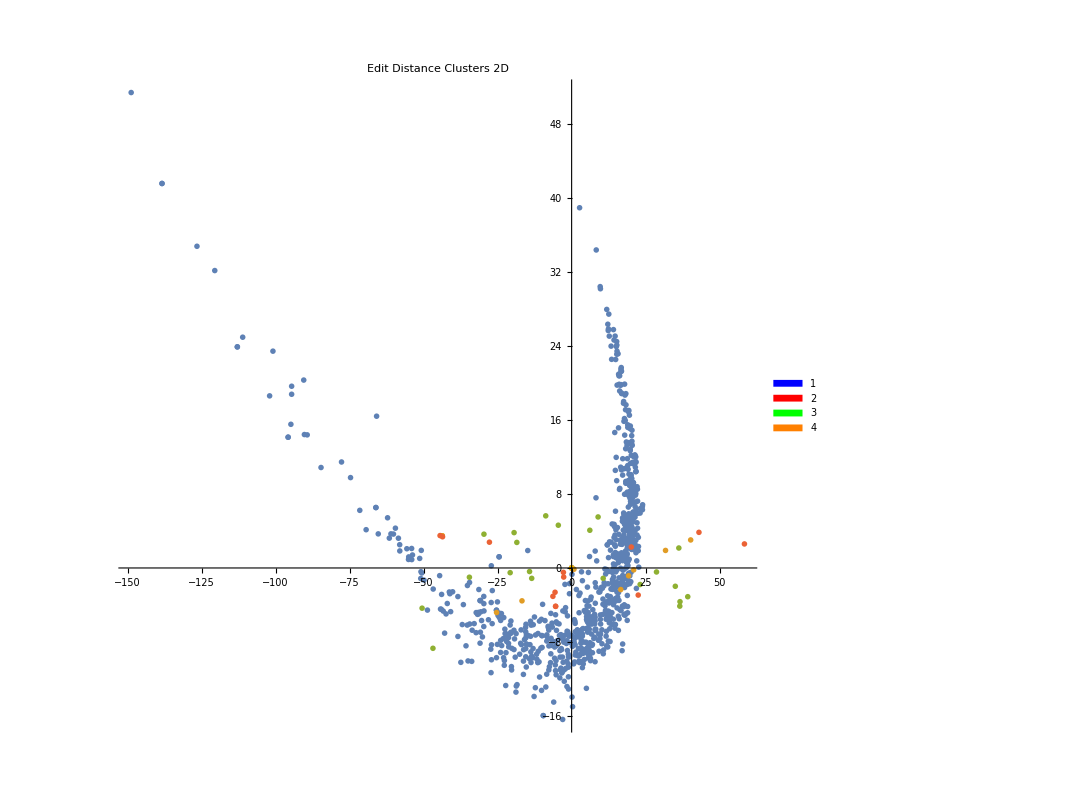

```mathematica
visualizeClustersFromData[ListAll,Classifier,2,"Edit Distance Clusters 2D"]
```

```mathematica
plot3D=visualizeClustersFromData[ListAll,Classifier,3,"Edit Distance Clusters 3D"]
```

-Graphics3D-

```mathematica
TitleClassifier=ClusterClassify[allTitles,DistanceFunction->EditDistance,PerformanceGoal->"Quality"]
```

```mathematica
(* Exporting the clustered titles below... *)
assocAllTitlesClusters=GatherBy[allTitles,TitleClassifier];
toExport=assocAllTitlesClusters;
For[cluster=1,cluster≤Length[toExport],cluster+=1,
Export[FileNameJoin[{NotebookDirectory[],"clustered by absolute edit distance",ToString[cluster]<>".csv"}],toExport[[cluster]]];
]
```

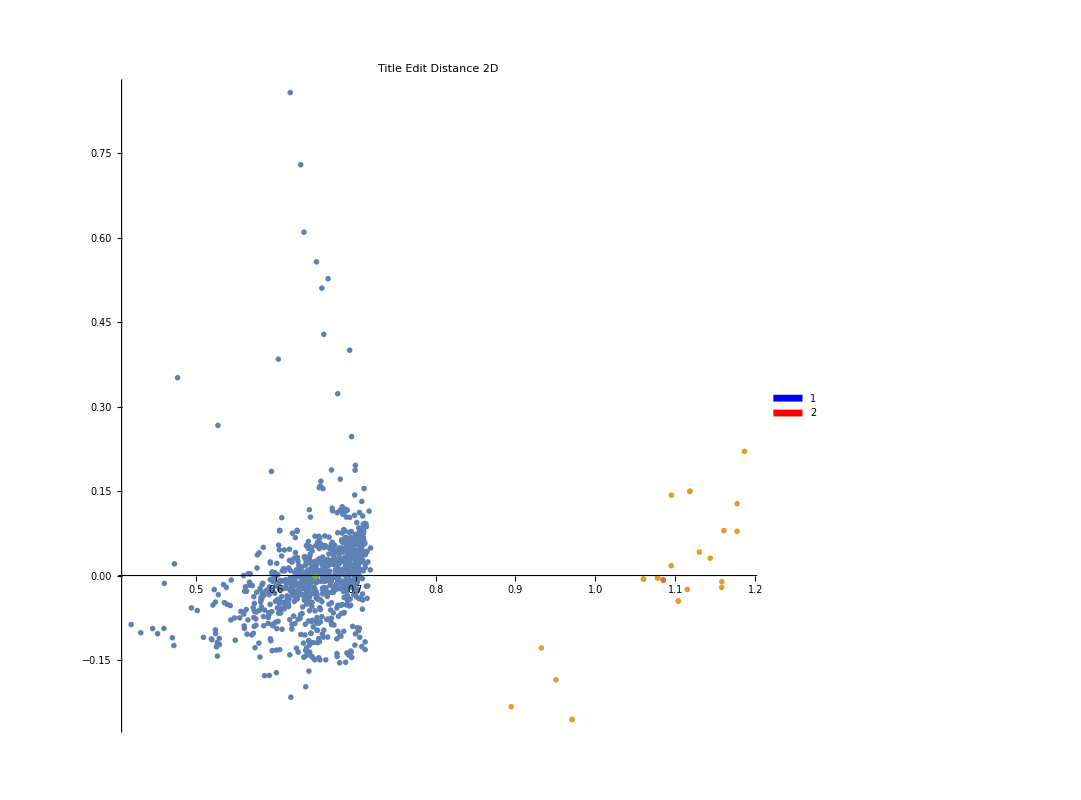

```mathematica
visualizeClustersFromData[allTitles,TitleClassifier,2,"Title Edit Distance 2D"]
```

```mathematica
visualizeClustersFromData[allTitles,TitleClassifier,3,"Title Edit Distance 3D"]
```

-Graphics3D-

```mathematica
(* Try extracting the boolean namespace vector and classify the data based on that. *)
```

```mathematica
binaryNamespaceFeaturesAllTitles=ParallelTable[If[StringContainsQ[allTitles[[title]],featureList[[feature]],IgnoreCase->True],True,False],{title,Length[allTitles]},{feature,Length[featureList]}];
```

```mathematica
namespaceFeaturesAllTitles=ParallelTable[If[StringContainsQ[allTitles[[title]],featureList[[feature]],IgnoreCase->True],1,0],{title,Length[allTitles]},{feature,Length[featureList]}];
namespaceFeaturesAllTitlesManhattanDistanceMatrix=ParallelTable[ManhattanDistance[namespaceFeaturesAllTitles[[title1]],namespaceFeaturesAllTitles[[title2]]],{title1,Length[allTitles]},{title2,Length[allTitles]}];
ArrayPlot[namespaceFeaturesAllTitlesManhattanDistanceMatrix,ColorFunction->"TemperatureMap", ImageSize->{Automatic,600},PlotLegends->Automatic]
```

-Graphics-

```mathematica
ManhattanMatrixNamespaceClassifier=ClusterClassify[namespaceFeaturesAllTitlesManhattanDistanceMatrix]
```

ClassifierFunction[…]

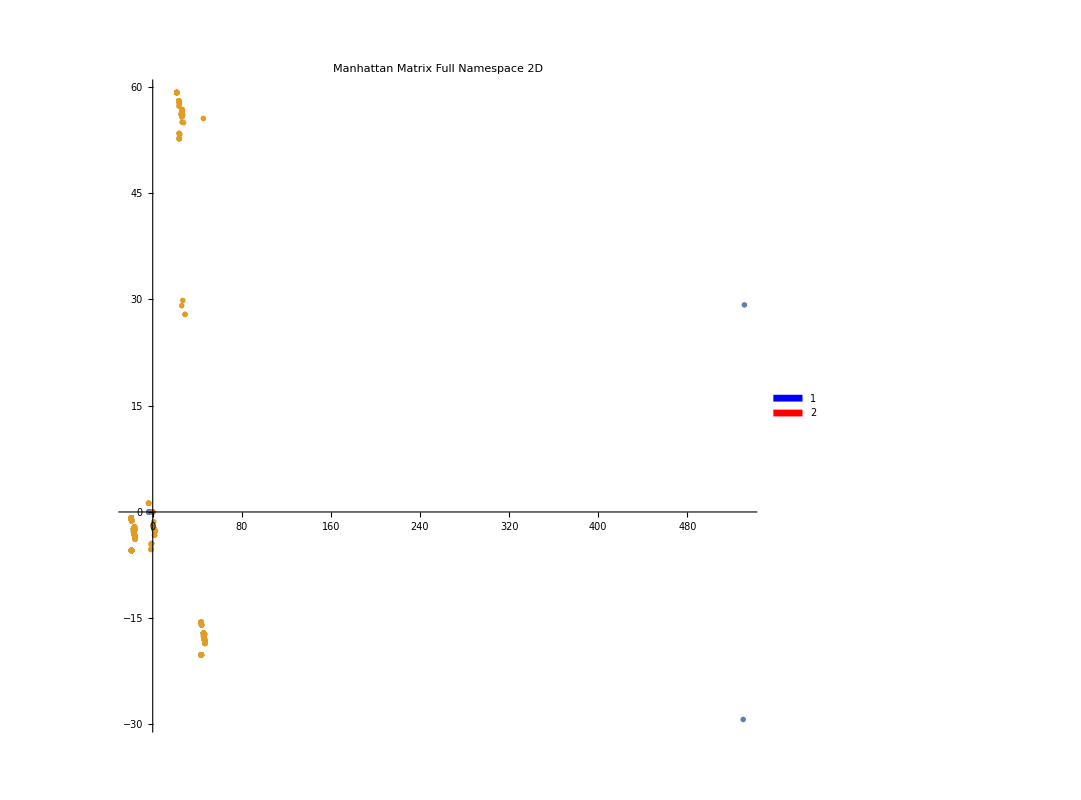

```mathematica
visualizeClustersFromData[namespaceFeaturesAllTitlesManhattanDistanceMatrix,ManhattanMatrixNamespaceClassifier,2,"Manhattan Matrix Full Namespace 2D"]
```

```mathematica
visualizeClustersFromData[namespaceFeaturesAllTitlesManhattanDistanceMatrix,ManhattanMatrixNamespaceClassifier,3,"Manhattan Matrix Full Namespace 3D"]
```

-Graphics3D-

```mathematica
NamespaceClassifier=ClusterClassify[binaryNamespaceFeaturesAllTitles]
```

ClassifierFunction[…]

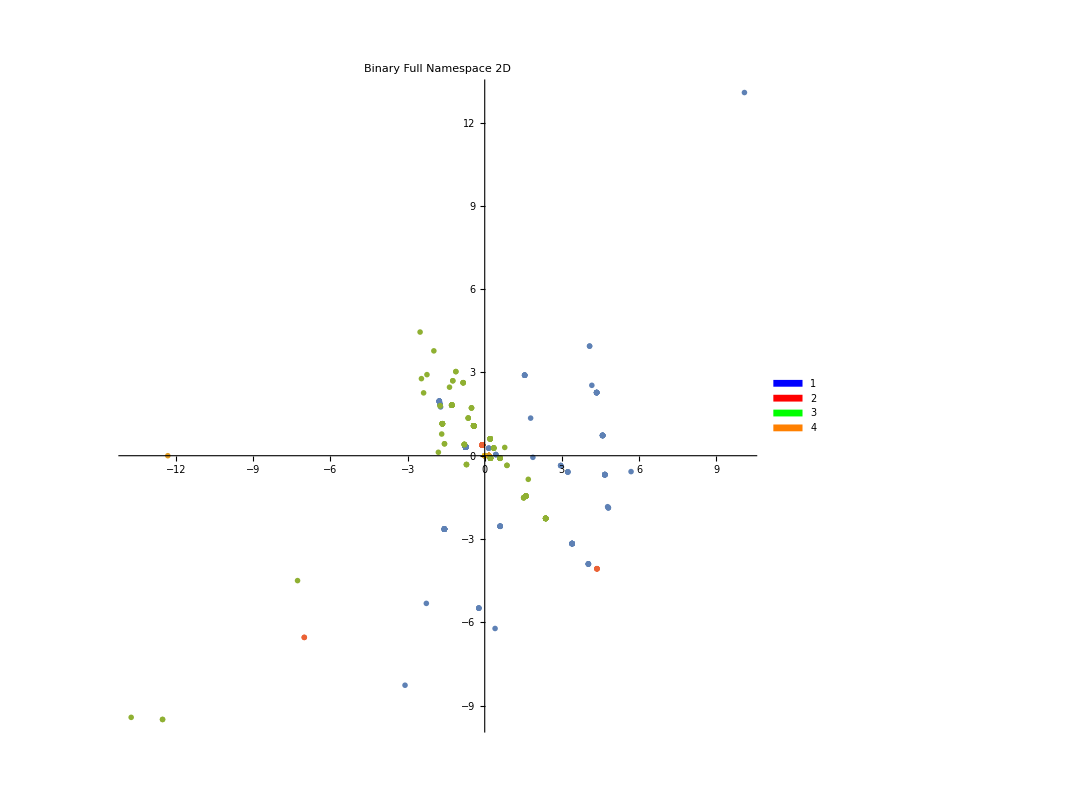

```mathematica
visualizeClustersFromData[binaryNamespaceFeaturesAllTitles,NamespaceClassifier,2,"Binary Full Namespace 2D"]
```

```mathematica
visualizeClustersFromData[binaryNamespaceFeaturesAllTitles,NamespaceClassifier,3,"Binary Full Namespace 3D"]
```

-Graphics3D-

```mathematica
assocBinaryNamespaceFeaturesAllTitles=Thread[{allTitles,binaryNamespaceFeaturesAllTitles}];
assocBinaryNamespaceFeaturesAllTitlesClusters=GatherBy[assocBinaryNamespaceFeaturesAllTitles,NamespaceClassifier[#[[2]]]&];
```

```mathematica
(* Exporting the clustered titles below... *)
toExport=assocBinaryNamespaceFeaturesAllTitlesClusters[[All,All,1]];
For[cluster=1,cluster≤Length[toExport],cluster+=1,
Export[FileNameJoin[{NotebookDirectory[],"clustered by full namespace feature vector",ToString[cluster]<>".csv"}],toExport[[cluster]]];
]
```

```mathematica
(* This constructs feature vectors by appending to each feature vector only features that are true per given title. *)
```

```mathematica
binaryNamespaceOnlyTrueFeaturesAllTitles=List[];
For[title=1,title≤Length[allTitles],title+=1,
titleFeatureList=List[];
For[feature=1,feature≤Length[featureList],feature+=1,
If[StringContainsQ[allTitles[[title]],featureList[[feature]],IgnoreCase->True],
(*Print["'"<>allTitles[[title]]<>"' contains "<>featureList[[feature]]];*)
AppendTo[titleFeatureList,featureList[[feature]]]
(*Print[titleFeatureList]]*)
]];
(*Print[titleFeatureList];*)
AppendTo[binaryNamespaceOnlyTrueFeaturesAllTitles,titleFeatureList]

]
```

```mathematica
binaryNamespaceOnlyTrueFeaturesAllTitles;
```

{{gen},{gen},{gen},{positive},{mutat,deletion},{gen,dna},{gen},{gen},{positive},{positive},{dna},{gen},{gen},{gen},{gen},{positive},{gen},{dna},{gen},{gen},{gen},{gen},{familial},{gen},{dna},{gen},{gen},{gen},{gen},{gen},{negative},{gen},{gen},{gen},{gen,sequenc},{gen},{gen},{gen},{negative},{gen},{gen},{gen},{gen,mutat},{gen},{familial},{gen,dna},{familial},{gen},{familial},{gen},{positive},{gen},{gen},{gen,sequenc,dna},{sequenc},{gen},{gen},{positive},{gen},{familial},{dna},{gen},{gen,variant},{dna},{gen},{dna},{mutat},{mutant},{gen},{gen},{gen},{gen},{dna},{sequenc},{gen},{gen},{gen,linkage},{negative},{dna},{gen,mutat},{gen,dna},{dna},{dna},{germ},{familial},{dna},{gen},{dna},{positive},{gen},{gen,dna},{gen},{positive,negative},{positive},{germ},{gen,dna},{mutat},{gen},{dna},{gen},{gen},{dna},{negative},{gen},{dna},{positive,negative},{negative},{positive},{dna},{dna},{dna},{familial},{positive},{positive},{positive},{gen,positive},{gen},{gen},{dna},{mutat,positive},{positive},{gen},{dna},{negative},{gen},{positive},{germ},{gen},{gen},{germ},{positive},{gen,dna},{gen,positive},{gen},{negative},{positive},{dna},{gen,dna},{gen},{negative},{positive,negative},{germ},{negative},{dna},{mutat,germ,negative},{positive},{gen},{gen,deletion},{germ},{gen},{gen,positive,negative},{gen},{positive},{sequenc},{gen},{germ},{positive},{mutant},{positive},{gen},{mutant},{positive},{insertion},{negative},{positive},{positive,negative},{positive},{mutat,negative,mutation-associated},{gen},{sequenc,dna},{positive,negative},{germ},{gen},{gen,positive,negative},{mutant},{dna},{positive},{positive},{familial},{negative},{gen},{dna},{positive,negative},{positive},{gen,dna},{gen,dna},{gen},{gen},{germ},{positive},{germ},{negative},{positive,negative},{germ},{germ},{gen},{deletion},{gen},{positive},{negative},{dna},{gen},{gen,linkage},{mutat},{mutant},{positive},{mutat},{positive},{mutat,positive},{gen},{intron},{autosomal},{positive},{gen},{gen},{mutat},{familial},{familial},{positive},{autosomal},{gen},{germ},{gen,positive},{gen,mutat},{mutat,insertion},{positive},{negative},{mutat},{germ},{gen,gene-modified},{gen,polymorphism},{mutat},{mutat,positive},{autosomal},{gen,mutat},{positive},{positive},{dna},{germ},{dna},{gen,positive},{variant},{positive},{negative},{positive},{mutat},{positive},{gen},{gen,dna},{gen},{dna},{gen},{gen},{gen,polymorphism},{mutat},{dna},{gen},{gen},{gen},{sequenc},{mutat},{gen},{dna},{gen},{gen},{gen,deletion},{dna},{gen},{gen},{positive},{mutat},{gen},{gen},{positive},{negative},{gen,deletion},{sequenc},{positive},{gen,negative},{gen,mutat},{gen},{gen},{mutat,deletion},{deletion},{gen},{intron},{gen,sequenc},{gen},{gen},{dna},{gen},{gen},{gen},{gen},{gen},{gen},{negative},{gen},{gen},{gen},{positive},{gen},{gen,variant},{gen,negative},{mutat,sequenc,exome},{mutat},{gen},{variant},{dna},{gen},{gen},{gen,allele},{gen},{negative},{gen},{gen,negative},{gen,linkage},{negative},{gen},{gen,negative},{gen},{sequenc},{dna},{mutat,sequenc,exome},{gen},{gen},{negative},{dna},{mutant},{positive},{dna},{intron},{negative},{gen},{deletion},{dna},{gen},{gen,familial,deletion},{gen},{gen},{gen},{gen},{gen,deletion},{gen},{gen},{gen},{gen},{dna},{gen},{gen,dna,snp},{gen},{gen,sequenc,dna},{positive},{positive},{gen,polymorphism},{gen,mutat},{gen},{gen},{gen,polymorphism},{dna},{gen},{gen,allele},{gen},{gen},{positive},{gen},{gen},{negative},{dna},{gen,variant},{deletion},{gen},{gen},{gen},{gen},{gen},{autosomal,mutat},{gen},{gen},{negative},{gen,positive,negative},{gen},{gen,snp},{gen},{dna},{mutat},{gen},{dna},{gen,mutant},{gen},{gen},{gen},{familial},{gen},{positive},{gen,sequenc},{gen},{mutat},{dna},{mutat},{gen},{polymorphism},{positive},{familial},{gen},{familial},{dna},{dna},{gen,mutat},{mutat},{gen},{gen},{sequenc,dna},{gen,variant},{gen,mutat},{gen},{polymorphism},{gen},{gen},{gen},{gen},{gen},{gen},{gen},{gen},{positive},{gen,mutat},{gen,mutat},{gen},{gen,mutat},{gen},{dna},{gen},{gen},{gen},{polymorphism},{negative},{gen},{gen,dna},{gen,sequenc},{gen},{gen},{gen},{gen},{gen},{gen,mutant,deletion},{gen},{gen,mutat,variant},{gen},{gen},{mutat},{mutat,positive},{linkage},{gen},{gen},{gen},{sequenc,deletion},{gen,dna},{positive},{dna},{gen,dna},{gen,sequenc},{gen},{negative},{gen},{gen},{allele,variant},{gen},{allele},{positive},{gen,sequenc},{sequenc,dna},{gen},{gen},{mutat},{gen},{dna},{negative},{gen},{dna},{gen},{gen},{gen},{negative},{gen},{gen,variant},{gen},{gen,mutat},{gen},{insertion},{mutant},{gen},{gen},{deletion},{dna},{allele},{gen},{gen},{gen},{gen},{gen,negative},{gen},{gen,dna},{mutant},{gen},{gen},{gen},{gen},{gen,mutat,dna},{gen,polymorphism},{dna},{negative},{negative},{sequenc},{gen,mutat},{dna},{mutat},{gen,deletion},{gen},{sequenc},{deletion},{gen,variant},{gen},{positive},{gen},{snp},{gen},{gen},{positive},{gen,germ},{dna},{gen,polymorphism},{dna,allele},{gen},{gen,sequenc,dna},{deletion},{dna},{gen,positive},{gen},{mutat},{gen,polymorphism},{gen},{gen},{negative},{gen},{gen},{gen},{gen,polymorphism},{gen},{gen,germ,variant},{gen},{dna},{gen},{gen},{mutat},{gen,mutat,deletion},{gen,negative},{gen},{gen},{gen},{mutat,homozygous},{gen},{dna},{gen},{gen},{dna},{dna},{gen},{polymorphism},{gen},{gen},{gen},{gen},{gen},{autosomal,gen},{negative},{gen},{dna},{dna},{gen},{gen},{gen,polymorphism},{gen},{gen},{gen},{gen,mutat},{dna},{deletion},{negative},{positive,negative},{gen,mutat},{gen},{mutat},{positive,negative},{mutat},{autosomal,gen},{mutat},{mutat,familial},{negative},{gen},{mutat,germ},{gen},{gen},{positive},{dna},{negative},{germ},{gen,germ},{gen},{dna},{gen},{gen},{positive},{dna},{dna},{gen,positive},{mutat,heterozygous},{gen},{gen,positive},{gen},{dna},{gen},{deletion},{gen},{dna},{gen},{gen},{sequenc},{gen,dna},{negative},{gen},{positive},{sequenc,dna},{mutat,germ},{gen},{gen},{gen,sequenc,allele},{gen},{gen},{dna},{gen},{gen},{autosomal,gen},{gen},{positive},{gen},{gen,dna},{negative},{gen,variant},{gen},{gen},{gen},{gen},{gen,mutat},{dna},{homozygous},{mutat},{dna},{gen},{dna},{gen,dna},{sequenc,dna},{gen,variant},{sequenc},{gen},{gen},{linkage},{negative},{mutat},{gen},{negative},{gen},{gen,positive},{negative},{gen},{gen},{positive},{gen,variant},{gen},{negative},{gen},{gen},{positive},{mutat},{gen},{deletion,heterozygous},{gen},{gen,dna,intron},{negative},{positive,negative},{dna},{gen},{gen,deletion},{gen},{gen,dna},{dna},{positive},{gen,sequenc,exome,variant},{gen},{mutat},{negative},{positive,sequenc},{gen},{dna},{gen,dna},{gen,germ},{mutat},{dna},{linkage},{gen},{gen},{gen,positive},{positive},{positive},{positive},{gen,mutat,germ},{gen},{mutat},{variant},{dna},{gen,mutant,deletion},{snp},{gen,familial},{mutat},{mutat},{gen},{gen},{sequenc},{insertion},{gen},{negative},{gen},{gen,dna},{negative},{positive},{variant},{gen},{mutant},{gen},{gen,variant,heterozygous},{gen},{gen},{gen,mutat,intron},{gen,sequenc},{gen},{gen,polymorphism},{mutat,heterozygous},{intron},{gen},{gen,mutat},{gen,dna},{sequenc},{gen},{gen},{gen},{gen},{gen},{gen,variant},{gen},{gen},{mutat},{gen},{gen,mutat},{gen,dna},{positive},{positive},{gen},{gen},{gen},{gen},{gen},{deletion},{linkage},{gen},{sequenc},{variant},{gen},{gen},{sequenc},{dna},{gen},{positive},{intron},{negative},{dna},{dna},{gen,positive},{variant},{gen,dna},{gen,variant},{negative},{negative},{gen},{gen,sequenc,dna},{gen,polymorphism},{dna},{dna},{gen},{negative},{dna},{gen},{gen},{gen},{gen},{gen},{allele},{gen},{gen,positive,negative},{gen},{gen,variant},{gen},{gen,mutat},{sequenc},{mutat,dna},{gen,variant},{gen},{dna},{polymorphism},{gen},{gen,germ,variant},{dna},{gen},{gen},{positive,negative},{mutat,negative},{mutat},{positive,negative},{mutat,germ},{dna},{positive},{negative},{mutant},{positive,negative},{positive},{negative},{gen,positive},{mutat,dna},{dna},{positive},{negative},{gen,positive},{positive},{mutat,positive},{mutat,positive},{gen},{positive,negative},{mutat},{gen,mutat},{gen,mutat},{positive},{positive},{mutat},{dna},{positive},{negative},{negative},{positive,negative},{mutat,positive},{mutat,negative},{positive,negative},{positive},{negative},{mutant},{mutat},{positive,negative},{positive,negative},{positive}}

```mathematica
Length[binaryNamespaceOnlyTrueFeaturesAllTitles]
```

867

```mathematica
(* This gives 34 classes with Agglomerate if not locked at 4 clusters max. All those clusters have been exported to "clustered by true features - long". *)
```

```mathematica
OnlyTrueFeaturesClassifier=ClusterClassify[binaryNamespaceOnlyTrueFeaturesAllTitles]
```

ClassifierFunction[…]

```mathematica
(* Exporting the clustered titles below... *)
```

```mathematica
assocOnlyTrueFeaturesAllTitles=Thread[{allTitles,binaryNamespaceOnlyTrueFeaturesAllTitles}];
assocOnlyTrueFeaturesAllTitlesClusters=GatherBy[assocOnlyTrueFeaturesAllTitles,OnlyTrueFeaturesClassifier[#[[2]]]&];
```

```mathematica
toExport=assocOnlyTrueFeaturesAllTitlesClusters;
For[cluster=1,cluster≤Length[toExport],cluster+=1,
Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"clustered by true features"}]];];
Export[FileNameJoin[{NotebookDirectory[],"clustered by true features",ToString[cluster]<>".csv"}],toExport[[cluster]]];
]
```

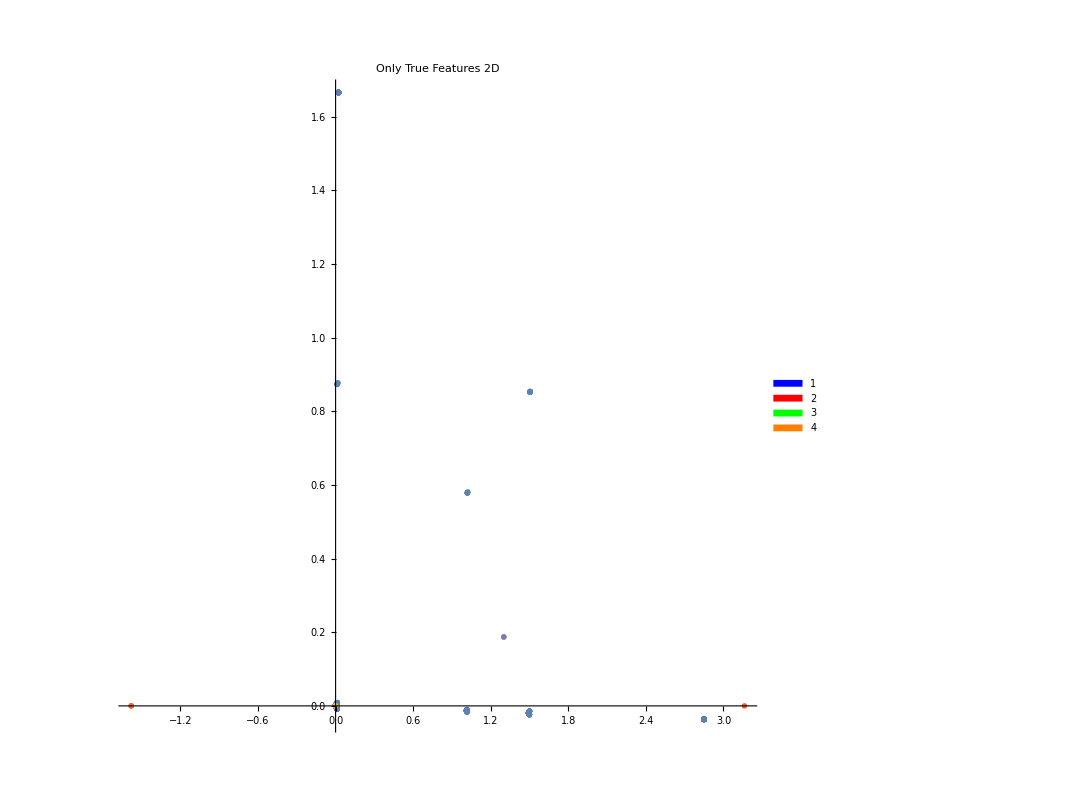

```mathematica
visualizeClustersFromData[binaryNamespaceOnlyTrueFeaturesAllTitles,OnlyTrueFeaturesClassifier,2,"Only True Features 2D"]
```

```mathematica
visualizeClustersFromData[binaryNamespaceOnlyTrueFeaturesAllTitles,OnlyTrueFeaturesClassifier,3,"Only True Features 3D"]
```

-Graphics3D-

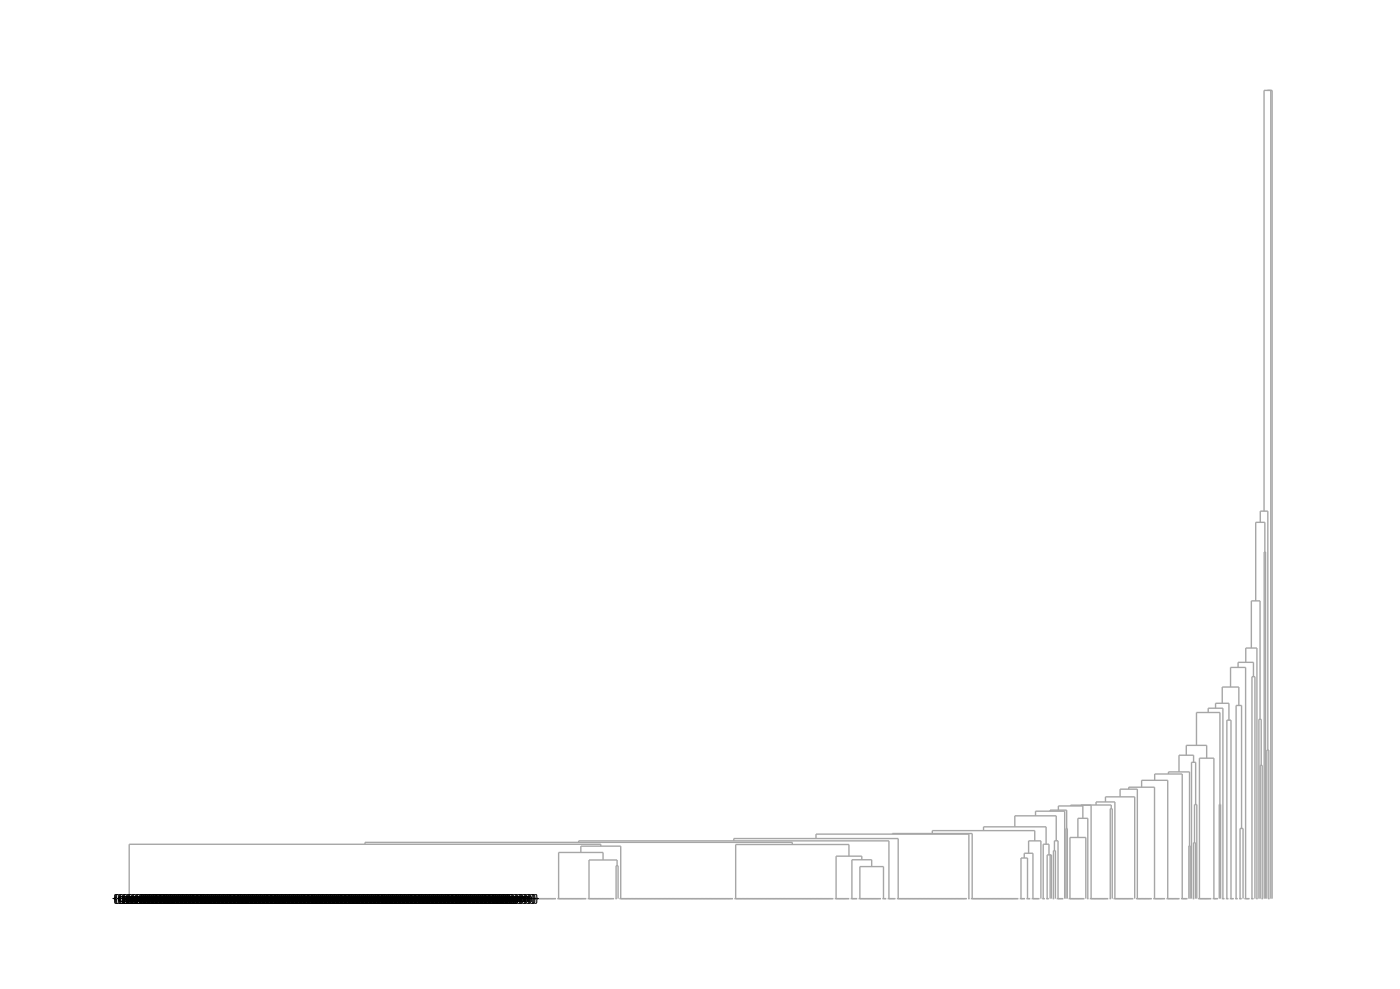

```mathematica
Dendrogram[binaryNamespaceOnlyTrueFeaturesAllTitles->(Rotate[ #,3 Pi/2]&/@binaryNamespaceOnlyTrueFeaturesAllTitles),ImageSize->1400]
```

```mathematica
(* Let's try with a random sample from each cluster? *)
```

{Common variation in the autism risk gene CNTNAP2, brain structural connectivity and multisensory speech integration,Hormonal Contraceptive Use Among HIV-Positive Women and HIV Transmission Risk to Male Partners, Zambia, 1994-2012,Mitochondrial tRNA(Phe) mutation as a cause of end-stage renal disease in childhood,A Phase II Trial of Pevonedistat and Azacitidine in MDS or MDS/MPN Patients Who Fail Primary Therapy With DNA Methyl Transferase Inhibitors}

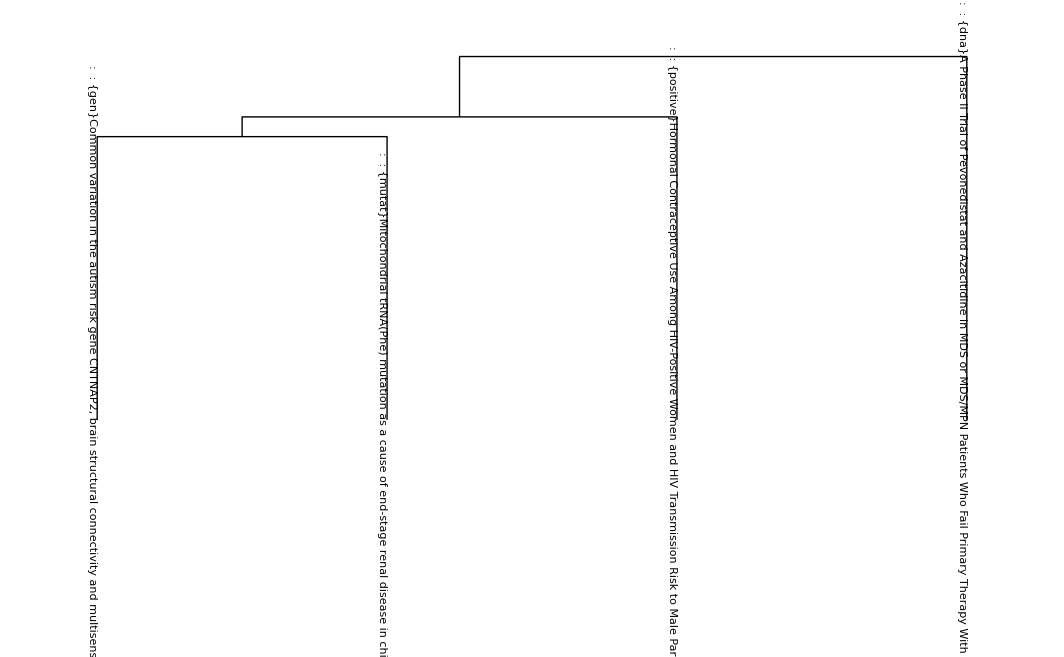

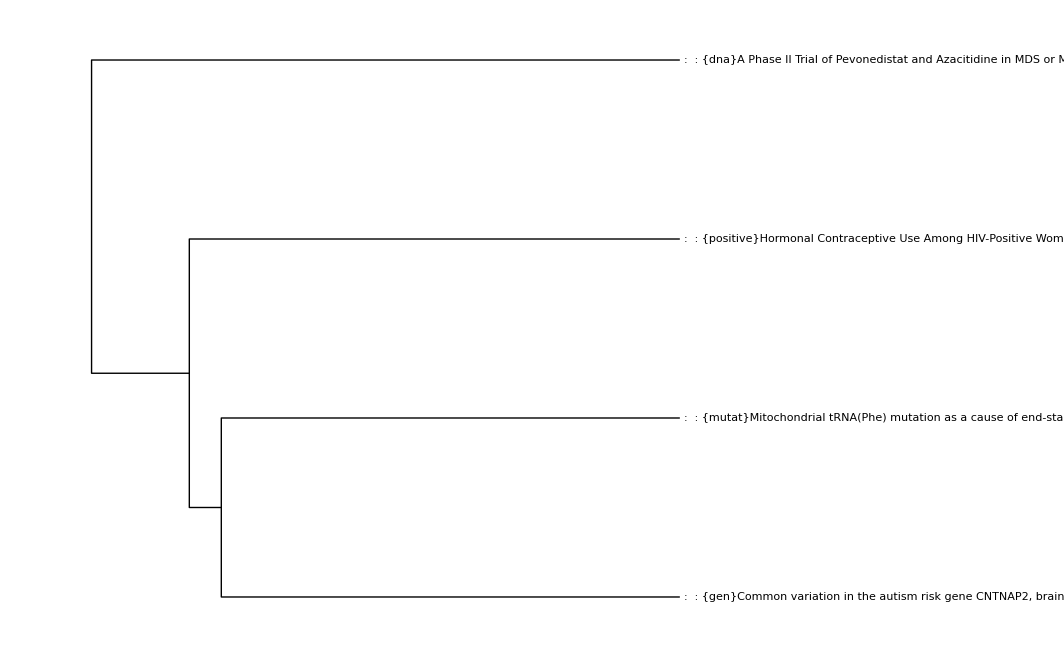

```mathematica
samples=1;
randomSamplesFromEachCluster=Flatten[RandomSample[#[[All,1]],samples]&/@assocOnlyTrueFeaturesAllTitlesClusters,1]
Off[Agglomerate::ties]
DendrogramPlot[randomSamplesFromEachCluster,LeafLabels->(Rotate[ Row[{getFromClusteredAssociationList[assocOnlyTrueFeaturesAllTitlesClusters,#],#}," : "],3 Pi/2]&/@randomSamplesFromEachCluster),Linkage->"WeightedAverage"]
DendrogramPlot[randomSamplesFromEachCluster,LeafLabels->(Rotate[ Row[{getFromClusteredAssociationList[assocOnlyTrueFeaturesAllTitlesClusters,#],#}," : "],0]&/@randomSamplesFromEachCluster),Linkage->"WeightedAverage",Orientation->Left]
```

```mathematica
(* This extracts only true features into a feature string instead of a vector.
UPDATE: This behaves exactly the same as the feature vector with string components. *)
```

```mathematica
binaryNamespaceOnlyTrueFeaturesAllTitlesString=List[];
For[title=1,title≤Length[allTitles],title+=1,
titleFeatureString="";
For[feature=1,feature≤Length[featureList],feature+=1,
If[StringContainsQ[allTitles[[title]],featureList[[feature]],IgnoreCase->True],
(*Print["'"<>allTitles[[title]]<>"' contains "<>featureList[[feature]]];*)
If[StringLength[titleFeatureString]==0,
titleFeatureString=featureList[[feature]],
titleFeatureString=(titleFeatureString<>" " <>featureList[[feature]])
]
(*Print[titleFeatureString];*)
]
];
(*Print[titleFeatureString];*)
AppendTo[binaryNamespaceOnlyTrueFeaturesAllTitlesString,titleFeatureString]
]
```

```mathematica
binaryNamespaceOnlyTrueFeaturesAllTitlesString;
```

```mathematica
(* This now tries to agglomerate and draw the dendrogram based upon the feature string. 
Note that the Agglomerate and DBSCAN methods for this output the exact same number of 
classes as the feature vector case 34 and 4 repectively. *)
```

```mathematica
OnlyTrueFeaturesStringClassifier=ClusterClassify[binaryNamespaceOnlyTrueFeaturesAllTitlesString,4,Method->"Agglomerate"]
```

ClassifierFunction[…]

```mathematica
assocOnlyTrueFeaturesAllTitlesString=Thread[{allTitles,binaryNamespaceOnlyTrueFeaturesAllTitlesString}];
assocOnlyTrueFeaturesAllTitlesClustersString=GatherBy[assocOnlyTrueFeaturesAllTitlesString,OnlyTrueFeaturesStringClassifier[#[[2]]]&];
```

```mathematica
(* There is a problem with sampling more than 1 title here because cluster 2 and 3 have 1 element each only. *)
```

{Docetaxel and Cyclophosphamide Compared to Anthracycline-Based Chemotherapy in Treating Women With HER2-Negative Breast Cancer,Cisplatin With or Without Veliparib in Treating Patients With Recurrent or Metastatic Triple-Negative and/or BRCA Mutation-Associated Breast Cancer With or Without Brain Metastases,Long-Term Follow-up Protocol for Subjects Treated With Gene-Modified T Cells,Identification of a novel mutation in a Chinese family with Nance-Horan syndrome by whole exome sequencing}

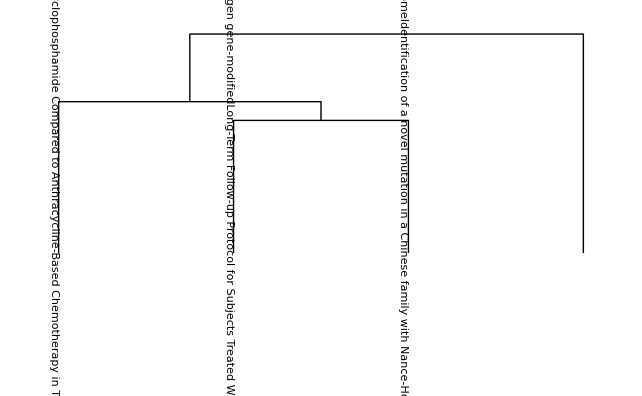

```mathematica
samples=1;
randomSamplesFromEachClusterString=Flatten[RandomSample[#[[All,1]],samples]&/@assocOnlyTrueFeaturesAllTitlesClustersString,1]
DendrogramPlot[randomSamplesFromEachClusterString,LeafLabels->(Rotate[ Row[{getFromClusteredAssociationList[assocOnlyTrueFeaturesAllTitlesClustersString,#],#}," : "],3 Pi/2]&/@randomSamplesFromEachClusterString),Linkage->"WeightedAverage"]
```

```mathematica
(* Here's what I think is the best version for the dendrogram after all this search.
Sample titles from the full boolean namespace clustering and call the dendrogram on those.
Then attach to the titles their only true feature vector and see how that dendrogram turns out. *)
(* This does not work around the issue I was facing with overfitting. The internal Agglomerate method
of the DendromgramPlot still classifies these titles into 34 classes, regardless of only being sampled from 4 clusters. *)
```

{Deletion of EP4 in S100a4-lineage cells reduces scar tissue formation during early but not later stages of tendon healing,The Genetic and Epigenetic Basis for FSHD,The clinical and genetic spectrum of catecholaminergic polymorphic ventricular tachycardia: findings from an international multicentre registry,Working with LGBT Individuals: Incorporating Positive Psychology into Training and Practice,A Study of Pertuzumab in Addition to Chemotherapy and Trastuzumab as Adjuvant Therapy in Participants With Human Epidermal Growth Receptor 2 (HER2)-Positive Primary Breast Cancer,High Rate of Positive Circumferential Resection Margins Following Rectal Cancer Surgery: A Call to Action,Direct antiglobulin ("Coombs") test-negative autoimmune hemolytic anemia: a review,Mice carrying a hypomorphic Evi1 allele are embryonic viable but exhibit severe congenital heart defects,Combination Chemotherapy With or Without Blinatumomab in Treating Patients With Newly Diagnosed BCR-ABL-Negative B Lineage Acute Lymphoblastic Leukemia,DNA methylation in blood as a mediator of the association of mid-childhood body mass index with cardio-metabolic risk score in early adolescence,An evaluation of statistical methods for DNA methylation microarray data analysis,DNA methyltransferase 3b regulates articular cartilage homeostasis by altering metabolism}

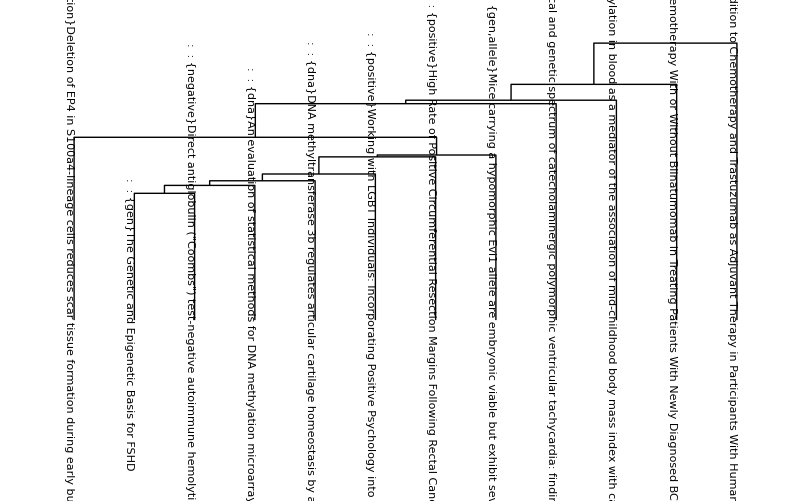

```mathematica
samples=3;
randomSamplesFromEachCluster=Flatten[RandomSample[#[[All,1]],samples]&/@assocBinaryNamespaceFeaturesAllTitlesClusters,1]
DendrogramPlot[randomSamplesFromEachCluster,LeafLabels->(Rotate[ Row[{getFromClusteredAssociationList[assocOnlyTrueFeaturesAllTitlesClusters,#],#}," : "],3 Pi/2]&/@randomSamplesFromEachCluster),Linkage->"WeightedAverage"]
```

```mathematica
namespaceFeaturesAllTitles=ParallelTable[If[StringContainsQ[allTitles[[title]],featureList[[feature]],IgnoreCase->True],1,0],{title,Length[allTitles]},{feature,Length[featureList]}];
```

```mathematica
Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"py"}]];];
Export[FileNameJoin[{NotebookDirectory[],"py","namespace_features.csv"}],namespaceFeaturesAllTitles];
```

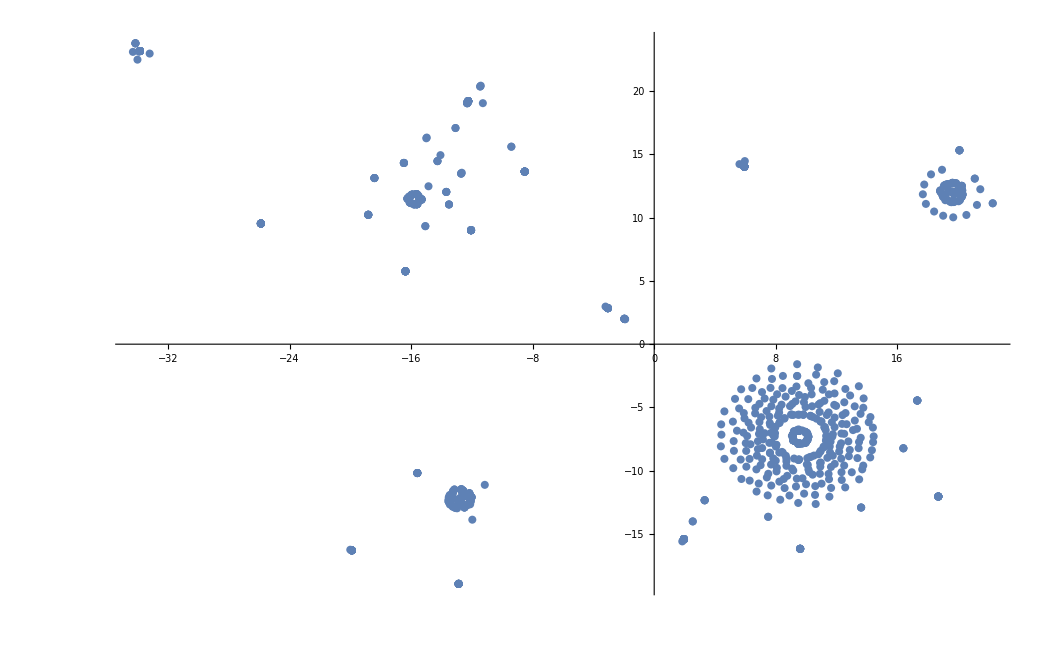

```mathematica
reducedNamespaceVectors=DimensionReduce[namespaceFeaturesAllTitles,Method->"TSNE", RandomSeeding->4];
ListPlot[reducedNamespaceVectors]
```

```mathematica
ReducedClusterer=ClusterClassify[reducedNamespaceVectors,Method->"GaussianMixture",DistanceFunction->EuclideanDistance]
```

ClassifierFunction[…]

```mathematica
clusters=GatherBy[reducedNamespaceVectors,ReducedClusterer];
```

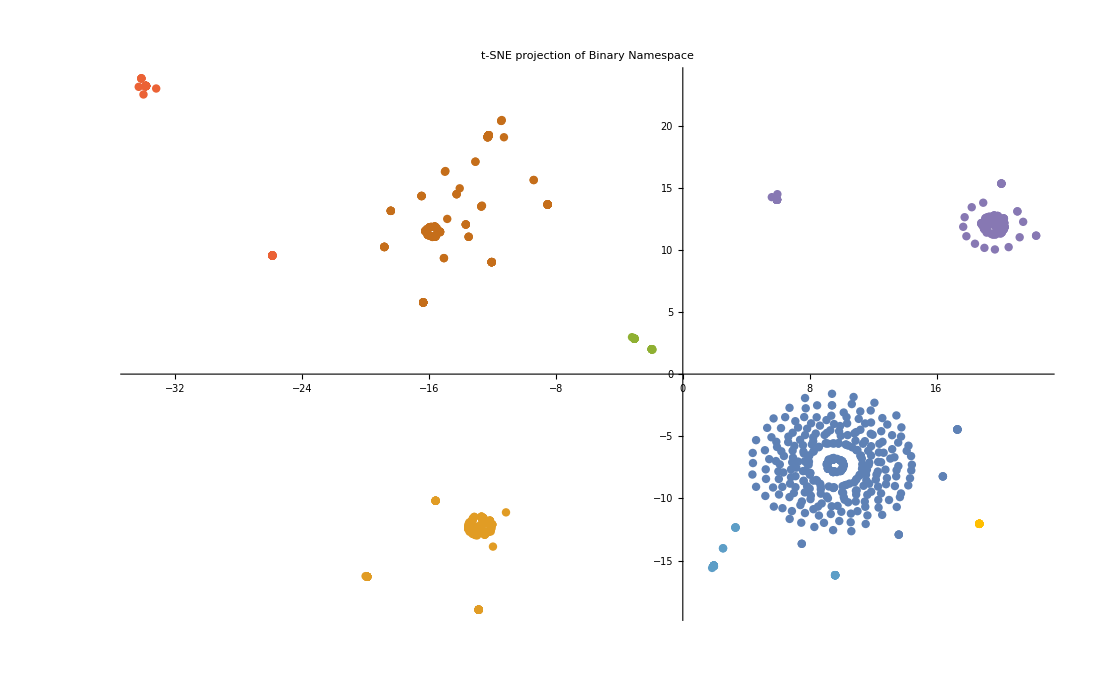

```mathematica
ListPlot[clusters,PlotLabel->Style["t-SNE projection of Binary Namespace","Subsubsection"]]
```

```mathematica
visualizeTSNE[reducedData_,classifier_,label_]:=Module[{K,allClusters,reducedAllCluster,reducedAllClusterCenters,listPlotData,coreColors,otherColorsCount,legendColors,classes,mrkCC,mrkCP,legend,markers},

(* This classifies the data into clusters given the classifier. *)
K=Length[ClassifierInformation[classifier,"Classes"]];(*Print[K];*)
listPlotData=GatherBy[reducedData,classifier];

classes=ClassifierInformation[classifier,"Classes"];
coreColors={Blue,Red,Green,Orange};
If[K<Length[coreColors],
coreColors=coreColors[[;;Abs[K]]];
];
otherColorsCount=K-Length[coreColors];
legendColors=coreColors;
If[otherColorsCount≠0,
AppendTo[legendColors,#]&/@RandomColor[otherColorsCount]
];

mrkCC=MapThread[Graphics[{#1,Style[Text[ToString[#2]],20,Bold]}]&,{legendColors,classes}];
mrkCP=MapThread[Graphics[{#,Disk[{0,0},ImageScaled[0.011]]}]&,{legendColors}];
legend=SwatchLegend[legendColors,classes,LegendMarkerSize->20];
markers=mrkCP;
AppendTo[markers,#]&/@mrkCC;
Return[ListPlot[listPlotData,PlotRange->All,ImageSize->800,AxesLabel->Automatic,PlotMarkers->markers,PlotLegends->legend,PlotLabel->label,LabelStyle->"Subsubsection"]];
]
```

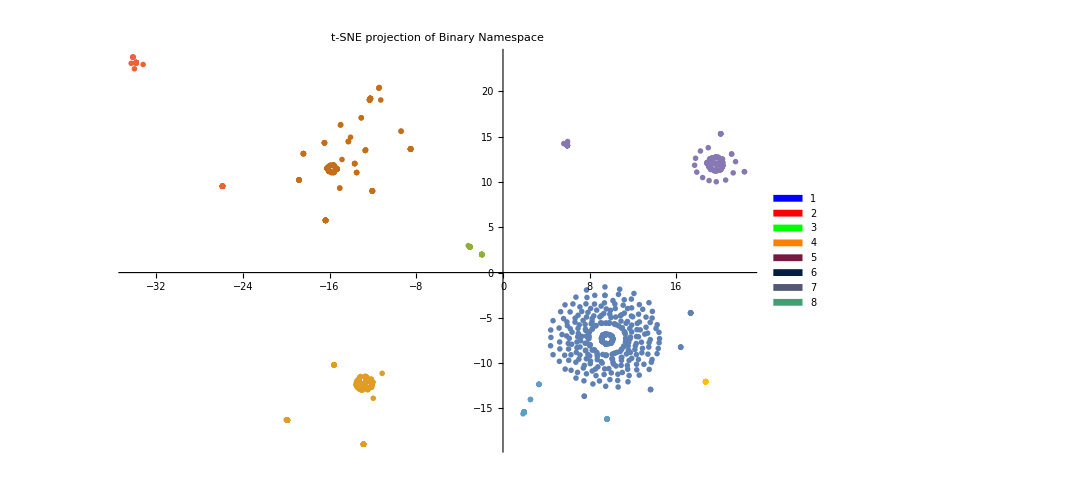

```mathematica
visualizeTSNE[reducedNamespaceVectors,ReducedClusterer,"t-SNE projection of Binary Namespace"]
```

```mathematica
reducedAssoc=Thread[{allTitles,reducedNamespaceVectors}];
```

```mathematica
reducedAssocClustered=GatherBy[reducedAssoc,ReducedClusterer[#[[2]]]&];
```

```mathematica
titleColor[reducedFeatures_]:=Which[
ReducedClusterer[reducedFeatures]==1,RGBColor[0.16,0.5,0.83],
ReducedClusterer[reducedFeatures]==2,RGBColor[0.94,0.43,0.32],
ReducedClusterer[reducedFeatures]==3,RGBColor[0.5,0.79,0.5],
ReducedClusterer[reducedFeatures]==4,RGBColor[1,0.82,0.41],
ReducedClusterer[reducedFeatures]==5,RGBColor[0.6,0,0.13],
ReducedClusterer[reducedFeatures]==6,RGBColor[0.04,0.18,1],
ReducedClusterer[reducedFeatures]==7,RGBColor[0.5,0,0.81],
ReducedClusterer[reducedFeatures]==8,RGBColor[0.74,1,0.5]
]
```

```mathematica
titleColorAssoc=titleColor[#[[2]]]&/@reducedAssoc
```

{RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.74, 1, 0.5],RGBColor[0.6, 0, 0.13],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.6, 0, 0.13],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.04, 0.18, 1],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[0.6, 0, 0.13],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[0.6, 0, 0.13],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.6, 0, 0.13],RGBColor[0.6, 0, 0.13],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.6, 0, 0.13],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[1, 0.82, 0.41],RGBColor[0.6, 0, 0.13],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.16, 0.5, 0.83],RGBColor[0.6, 0, 0.13],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.6, 0, 0.13],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.6, 0, 0.13],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.74, 1, 0.5],RGBColor[0.6, 0, 0.13],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[0.6, 0, 0.13],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.6, 0, 0.13],RGBColor[0.6, 0, 0.13],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[1, 0.82, 0.41],RGBColor[0.6, 0, 0.13],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.6, 0, 0.13],RGBColor[0.6, 0, 0.13],RGBColor[0.94, 0.43, 0.32],RGBColor[0.74, 1, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[1, 0.82, 0.41],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.6, 0, 0.13],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0, 0.81],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.16, 0.5, 0.83],RGBColor[0.6, 0, 0.13],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0, 0.81],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.74, 1, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.74, 1, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.74, 1, 0.5],RGBColor[0.74, 1, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.74, 1, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.74, 1, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.74, 1, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0, 0.81],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0, 0.81],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.04, 0.18, 1],RGBColor[0.74, 1, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.04, 0.18, 1],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.74, 1, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.74, 1, 0.5],RGBColor[0.6, 0, 0.13],RGBColor[1, 0.82, 0.41],RGBColor[0.16, 0.5, 0.83],RGBColor[0.6, 0, 0.13],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.04, 0.18, 1],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.74, 1, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[0.5, 0, 0.81],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.74, 1, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.74, 1, 0.5],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.04, 0.18, 1],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0, 0.81],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[0.74, 1, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0, 0.81],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0, 0.81],RGBColor[0.94, 0.43, 0.32],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.74, 1, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0, 0.81],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[0.74, 1, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.6, 0, 0.13],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.74, 1, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.6, 0, 0.13],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.16, 0.5, 0.83],RGBColor[0.6, 0, 0.13],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[0.5, 0.79, 0.5],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.6, 0, 0.13],RGBColor[0.16, 0.5, 0.83],RGBColor[0.04, 0.18, 1],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.74, 1, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.74, 1, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.6, 0, 0.13],RGBColor[0.04, 0.18, 1],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.74, 1, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0, 0.81],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.6, 0, 0.13],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.6, 0, 0.13],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.74, 1, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.6, 0, 0.13],RGBColor[0.04, 0.18, 1],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.6, 0, 0.13],RGBColor[0.5, 0, 0.81],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.04, 0.18, 1],RGBColor[0.94, 0.43, 0.32],RGBColor[0.16, 0.5, 0.83],RGBColor[0.5, 0.79, 0.5],RGBColor[0.94, 0.43, 0.32],RGBColor[0.04, 0.18, 1],RGBColor[0.16, 0.5, 0.83],RGBColor[0.94, 0.43, 0.32],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.6, 0, 0.13],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.94, 0.43, 0.32],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.16, 0.5, 0.83],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[0.5, 0.79, 0.5],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41],RGBColor[1, 0.82, 0.41]}

```mathematica
allTitlesColorized=Style[#[[1]],titleColor[#[[2]]]]&/@reducedAssoc;
```

```mathematica
Labeled[Framed[Pane[Grid[Transpose[{Range[Length[reducedAssoc]],allTitlesColorized}],Alignment->Left],Scrollbars->True,ImageSize->{Automatic,400}]],"All titles cluster-colorized",Top]
```

1 | Cell-specific gene delivery methods for expression and silencing in the lung
2 | Regulating genomic fidelity and cancer progression
3 | Genetic components of adverse effects of cisplatin therapy
4 | A Phase 1 Trial of SGN-CD70A in Patients with CD70 Positive Malignancies
5 | A Phase II Study of Ofatumumab-High Dose Methylprednisolone Followed by Ofatumumab-Alemtuzumab in 17p Deletion or TP53 Mutated CLL
6 | The indentification of a DNA viability window for the use of formalin-fixed paraffin-embedded tissue in comparative genomic hybrid micro
7 | NYS Genetic Screening and Counseling Programs
8 | Genetic control of recombination rate differences between Drosophila species
9 | A Ph 3 Open-Label Randomized Study of Quizartinib (AC220) Monotherapy vs Salvage Chemotherapy in Sbjs w/ FLT3-ITD Positive Acute Myeloid Leukemia (AML
10 | A Ph 3 Open-Label Randomized Study of Quizartinib (AC220) Monotherapy vs Salvage Chemotherapy in Sbjs w/ FLT3-ITD Positive Acute Myeloid Leukemia (AML
11 | Molecular mechanisms of DNA damage and histone modifications by cigarette smoke-induced lung cellular senescence
12 | Systems Genetics of Osteoblast Activity
13 | Statistical Methods for Estimation of Gene Regulatory Networks
14 | Genetic and Hormonal Mechanisms of Sex Differences in the Nervous System
15 | Cytoplasmic Trafficking of Non-viral Gene Therapy Vectors
16 | A Phase II Single-Arm Study of Regorafenib Maintenance Therapy in Patients with T3, T4 or Node-Positive Rectal Cancer Patients who completed Curative-
17 | Gene Targeting to Endogenous Stem Cells for Segmental Bone Fracture Healing
18 | Brg1-mediated repair of oxidative DNA double strand breaks in cardiomyocytes
19 | Exercise in Genetic Cardiovascular Disease
20 | Genetic screen for fungal triggers of the NLRP3-inflammasome in macrophages
21 | Yeast Genetic Approach to Enhance the Immunogenicity of HIV Envelope Glycoprotein
22 | The Genetic and Epigenetic Basis for FSHD
23 | Patients with Familial Hypercholesterolemia Sharing Goals and Difficult Decisions
24 | DISSERTATION RESEARCH:  The Genomic Nature of Adaption in Anolis Lizards
25 | Natural Trap Cave Revisited:  Ancient DNA, Climate and the Megafaunal Extinction
26 | The Genetics of Natural Variation in Memory Retention in Nasonia
27 | Genetic Susceptibility and Biomarkers of Platinum-related Toxicities
28 | Genetic Susceptibility and Biomarkers of Platinum-related Toxicities
29 | Genetic Susceptibility and Biomarkers of Platinum-related Toxicities
30 | Genetics and genomics of congenital heart disease and associated neurodevelopmental abnormalities
31 | Dalbavancin & vancomycin liofilchem MIC testing strip (MTS) 510 (k) testing site:  S. aureus & E. faecalis - Gram Negative - 2 Liofilchem MIC Testing
32 | Genetic Modification of Radiation Injury In Prostate Cancer Patients Treated with Radiotherapy
33 | Characterizing the Molecular and Developmental Basis of Environmental vs Genetic Trait Variation in Aphids
34 | MD-CPHG-Systems Genetics of Osteoblast Activity
35 | Development and Validation of Laboratory Procedures Using Next Generation Sequencing Technoligies To Assess Genes Causing Severe Com...
36 | Genetic Modification of Radiation InjuryIn Prostate Cancer Patients Treated with Radiotherapy
37 | Linking Genotype to Phenotype In Human FSHD Muscle Biopsies and Mouse Muscle Expressing DUX4 Protein
38 | Genetic Modifiers of Methylmercury Toxicity
39 | Ribonuclease E a novel new Gram-negative antimicrobial target
40 | Deveopment of a gene therapy approach to treat acute lung injury using a preclinical, large animal model
41 | Structural Control of Human Co-Factors for Retrovival Gene Expression
42 | Structural Control of Human Co-Factors for Retroviral Gene Expression
43 | A single genomic assay for HIV incidence and transmitted drug resistance mutation screening
44 | Hypercalciuria and Bone Quality in the Genetic Hypercalciuric Stone-Forming Rats
45 | Educating Patients and Care Providers About Familial Hypercholesterolemia Using EPIC
46 | The evolutionary and functional genomics of satellite DNA
47 | University of Rochester Site of the CASCADE Familial Hypercholesterolemia Registry
48 | Genetic and pharmacological manipulations of epigenetic aging
49 | The Familial Hypercholesterolemia Foundation CASCADE-FH Registry
50 | Administrative Coordinating Center: Cardiovascular Development and Pediatric Cardian Genomics Consortia-CHD Brain and Genes Protocol
51 | Inhibitor-2 is a positive regulator for PP1's synaptic and cognitive functions
52 | Development and Validation of a Gene Expression Assay to Predict the Risk of Recurrence Disease in Cutaneous Squamous Cell Carcinoma
53 | Genetic Analysis of Myotonic Dystrophy
54 | Genomic DNA extraction, sequencing and quantitative analysis of microbiome composition
55 | Multiplex Alternative Splice Sequencing (MASseq) of Ionis 598769 CS2 Samples
56 | HITI-Mediated Gene Editing for RYR1 Myopathy
57 | Genomic Study of Gestational Length and Associated Pregnancy Outcomes
58 | Novel effector protein functions encoded by T3SS positive V. cholerae
59 | Genetic Variation, Stress and Functional Outcomes After Stroke Rehabilitation
60 | Patients With Familial Hypercholesterolemia Sharing Goals and Difficult Decisions
61 | A Phase II Trial of Pevonedistat and Azacitidine In MDS or MDS/MPN Patients Who Fail Primary Therapy With DNA Methyl Transferase Inhibitors
62 | Population genomic variation, functional biology, and the risk of venous thrombosis
63 | Genetic Variant-Based Drug Discovery Targeting Conserved Pathways of Aging
64 | DNA Damage Response in Latent HIV-1 Reservoirs
65 | Genetic susceptibility to developmental neurotoxicity of methylmercury in Fish - MercuryGen II
66 | Pilot Study to Evaluate Circulating Tumor DNA In Follicular Lymphoma
67 | Expanded Access Program for Ivosidenib Monotherapy in Patients with Relapsed of Refractory Acute Myeloid Leukemia With an IDH1 Mutation
68 | Restoring Mutant P53 Function in B-Cell Lymphoma
69 | Model system of oral contraceptive-induced VTE:  integrating genomic, transcriptomic, and proteomic discovery with functional biology
70 | PPP2R5D Gene Variation (Jordan's Syndrome)
71 | Role of coronary artery disease risk gene JCAD in endothelial function and atherosclerosis
72 | Combining Genomic and Clinic Variables To Predict Radiation Toxicity in Localized Cancer Patients Via Machine Learning
73 | Validation of Cross-Species Biomarkers of DNA Damage
74 | Pulse Sequence & Image Reconstruction Software Exchange Agreement for Sequences from Charite - Universitatsmedizin Berlin
75 | Ozone Cardiovascular Effects in Genetically Susceptible People
76 | Long QT Syndrome-Population Genetics and Cardiac Studies
77 | Emergency Linkage to Outpatient Psychiatric Services
78 | ConfirmMDx Assay in Multiparametric MRI (mpMRI) PIRADS Scored Lesions After a Negative MR/US Fusion Biopsy
79 | Measuring Alterations of DNA in Human Blood
80 | Improving Risk Assessment of AML With a Precision Genomic Strategy to Assess Mutation Clearance
81 | Evaluating the Safety and Immunogenicity of EnvSeq-1 Envs Adjuvanted With GLA-SE, Administered Alone or With DNA Mosaic-Tre Env, in Healthy, HIV-Uninfected Adults
82 | Evaluating the Safety of and Immune Response to HIV-MAG DNA Vaccine With or Without Plasmid IL-12 Adjuvant Delivered Intramuscularly Via Electroporation Followed by VSV-gag HIV Vaccine Boost in Healthy, HIV-Uninfected Adults
83 | Evaluating the Safety and Immune Response to Different Combinations of the DNA-HIV-PT123 and AIDSVAX® B/E Vaccines in Healthy, HIV-Uninfected Adults
84 | Radiation Therapy Compared With Chemotherapy and Radiation Therapy in Treating Patients With Newly Diagnosed Primary Central Nervous System (CNS) Germ Cell Tumor
85 | The Effect of Diflunisal on Familial Amyloidosis
86 | Safety of and Immune Response to a DNA Vaccine and a Recombinant HIV-1-MVA Vaccine, Separately and in Combination, in Healthy Adults
87 | Parkinson's Research: The Organized Genetics Initiative
88 | Safety of and Immune Response to an HIV Preventive Vaccine (HIV-1 Gag DNA Alone or With IL-15 DNA) Given With or Without 2 Different Booster Vaccinations in HIV Uninfected Adults
89 | Study Evaluating SKI-606 (Bosutinib) In Philadelphia Chromosome Positive Leukemias
90 | Genetic Determinants of Barrett's Esophagus and Esophageal Adenocarcinoma
91 | Evaluating the Safety and Immunogenicity of PENNVAX®-GP DNA Vaccine and IL-12 Plasmid, Delivered Via Intradermal or Intramuscular Electroporation in Healthy, HIV-Uninfected Adults
92 | Environmental and Genetic Risk Factors for Pediatric Multiple Sclerosis
93 | PALbociclib CoLlaborative Adjuvant Study: A Randomized Phase III Trial of Palbociclib With Standard Adjuvant Endocrine Therapy Versus Standard Adjuvant Endocrine Therapy Alone for Hormone Receptor Positive (HR+) / Human Epidermal Growth Factor Receptor 2 (HER2)-Negative Early Breast Cancer
94 | A Study to Compare the Use of Fluconazole as Continuous Therapy Versus Periodic Therapy in HIV-Positive Patients With Recurrent Thrush
95 | Combination Chemotherapy Plus Amifostine in Treating Children With Malignant Germ Cell Tumors
96 | Safety and Effectiveness of HIV-1 DNA Plasmid Vaccine and HIV-1 Recombinant Adenoviral Vector Vaccine in HIV-Uninfected, Circumcised Men and Male-to-Female (MTF) Transgender Persons Who Have Sex With Men
97 | Olaparib Maintenance Monotherapy in Patients With BRCA Mutated Ovarian Cancer Following First Line Platinum Based Chemotherapy.
98 | Genetics of Charcot Marie Tooth (CMT) - Modifiers of CMT1A, New Causes of CMT2
99 | Pevonedistat and Azacitidine in MDS or MDS/MPN Patients Who Fail Primary Therapy With DNA Methyl Transferase Inhibitors
100 | Genetic Testing in Screening Patients With Stage IB-IIIA Non-Small Cell Lung Cancer That Has Been or Will Be Removed by Surgery (The ALCHEMIST Screening Trial)
101 | Genetic and Physical Characteristics of Rett Syndrome
102 | Safety of and Immune Response to a DNA HIV Vaccine Followed By Boosting With One of Two Serotypes of Adenoviral Vector HIV Vaccine in Healthy Adults
103 | Hormone Therapy With or Without Combination Chemotherapy in Treating Women Who Have Undergone Surgery for Node-Negative Breast Cancer (The TAILORx Trial)
104 | Targeted Therapy Directed by Genetic Testing in Treating Patients With Advanced Refractory Solid Tumors, Lymphomas, or Multiple Myeloma (The MATCH Screening Trial)
105 | Combination Chemotherapy With or Without Atezolizumab in Treating Patients With Stage III Colon Cancer and Deficient DNA Mismatch Repair
106 | Doxorubicin Hydrochloride, Cyclophosphamide, and Paclitaxel With or Without Bevacizumab in Treating Patients With Lymph Node-Positive or High-Risk, Lymph Node-Negative Breast Cancer
107 | Aspirin in Preventing Recurrence of Cancer in Patients With HER2 Negative Stage II-III Breast Cancer After Chemotherapy, Surgery, and/or Radiation Therapy
108 | Lung-MAP: Talazoparib in Treating Patients With HRRD Positive Recurrent Stage IV Squamous Cell Lung Cancer
109 | Abiraterone/Prednisone, Olaparib, or Abiraterone/Prednisone + Olaparib in Patients With Metastatic Castration-Resistant Prostate Cancer With DNA Repair Defects
110 | One-Time DNA Study for Vasculitis
111 | An Evaluation of a Multi-target Stool DNA (Mt-sDNA) Test, Cologuard, for CRC Screening in Individuals Aged 45-49 and at Average Risk for Development of Colorectal Cancer: Act Now
112 | Familial Intracranial Aneurysm Study II
113 | Lung-MAP: AZD4547 as Second-Line Therapy in Treating FGFR Positive Patients With Recurrent Stage IV Squamous Cell Lung Cancer
114 | S1400B Lung-MAP: Taselisib as Second-Line Therapy in Treating Patients With Recurrent Stage IV Squamous Cell Lung Cancer and Positive Biomarker Matches
115 | Letrozole in Treating Postmenopausal Women Who Have Received Hormone Therapy for Hormone Receptor-Positive Breast Cancer
116 | Lung-MAP: Palbociclib as Second-Line Therapy in Treating Cell Cycle Gene Alteration Positive Patients With Recurrent Stage IV Squamous Cell Lung Cancer
117 | Genomics Used to Improve DEpression Decisions
118 | Targeted Therapy Directed by Genetic Testing in Treating Pediatric Patients With Relapsed or Refractory Advanced Solid Tumors, Non-Hodgkin Lymphomas, or Histiocytic Disorders (The Pediatric MATCH Screening Trial)
119 | Safety of and Immune Response to a DNA HIV Vaccine (pGA2/JS7) Boosted With a Modified Vaccinia HIV Vaccine (MVA/HIV62) in Healthy Adults
120 | S1403, Afatinib Dimaleate With or Without Cetuximab in Treating Patients With Newly Diagnosed Stage IV or Recurrent, EGFR Mutation Positive Non-small Cell Lung Cancer
121 | Lung-MAP: Rilotumumab and Erlotinib Hydrochloride or Erlotinib Hydrochloride Alone as Second-Line Therapy in Treating Patients With Recurrent Stage IV Squamous Cell Lung Cancer and Positive Biomarker Matches
122 | Identifying Genetic Determinants of Eczema Herpeticum and Other Viral Infections in Individuals With Atopic Dermatitis
123 | Mycobacterial Cell Wall-DNA Complex in Treatment of BCG-refractory Patients With Non-muscle Invasive Bladder Cancer
124 | Docetaxel and Cyclophosphamide Compared to Anthracycline-Based Chemotherapy in Treating Women With HER2-Negative Breast Cancer
125 | Nitazoxanide Plus Ribavirin and Peginterferon for Therapy of Treatment Naive HCV Genotype 1 and HIV Coinfected Subjects
126 | Comparison of Axillary Lymph Node Dissection With Axillary Radiation for Patients With Node-Positive Breast Cancer Treated With Chemotherapy
127 | Chemotherapy Followed by Radiation Therapy in Treating Younger Patients With Newly Diagnosed Localized Central Nervous System Germ Cell Tumors
128 | Ensartinib in Treating Patients With Relapsed or Refractory Advanced Solid Tumors, Non-Hodgkin Lymphoma, or Histiocytic Disorders With ALK or ROS1 Genomic Alterations (A Pediatric MATCH Treatment Trial)
129 | Exercise in Genetic Cardiovascular Conditions
130 | Surgery and Combination Chemotherapy in Treating Children With Extracranial Germ Cell Tumors
131 | A Study of Pertuzumab in Addition to Chemotherapy and Trastuzumab as Adjuvant Therapy in Participants With Human Epidermal Growth Receptor 2 (HER2)-Positive Primary Breast Cancer
132 | Olaparib in Treating Patients With Relapsed or Refractory Advanced Solid Tumors, Non-Hodgkin Lymphoma, or Histiocytic Disorders With Defects in DNA Damage Repair Genes (A Pediatric MATCH Treatment Trial)
133 | Palbociclib in Treating Patients With Relapsed or Refractory Rb Positive Advanced Solid Tumors, Non-Hodgkin Lymphoma, or Histiocytic Disorders With Activating Alterations in Cell Cycle Genes (A Pediatric MATCH Treatment Trial)
134 | Genetic Susceptibility Biomarkers in Children With Neuroblastoma (Also Known as Neuroblastoma Epidemiology in North America [NENA])
135 | Platinum Based Chemotherapy or Capecitabine in Treating Patients With Residual Triple-Negative Basal-Like Breast Cancer Following Neoadjuvant Chemotherapy
136 | Exemestane With or Without Entinostat in Treating Patients With Recurrent Hormone Receptor-Positive Breast Cancer That is Locally Advanced or Metastatic
137 | Individualized Treatment in Treating Patients With Stage II-IVB Nasopharyngeal Cancer Based on EBV DNA
138 | DNA Variations in the Gene in Young Patients With Wilms' Tumor
139 | An Observational Study of Peginterferon (e.g. Pegasys)-Based Direct Acting Antiviral Triple Therapy in Patients With Chronic Hepatitis C Genotype 1
140 | Doxorubicin Hydrochloride and Cyclophosphamide Followed by Paclitaxel With or Without Carboplatin in Treating Patients With Triple-Negative Breast Cancer
141 | Doxorubicin Hydrochloride, Cyclophosphamide, and Pacltaxel With or Without Trastuzumab in Treating Women With HER2-Positive Node-Positive or High-Risk Node-Negative Breast Cancer
142 | Active Surveillance, Bleomycin, Carboplatin, Etoposide, or Cisplatin in Treating Pediatric and Adult Patients With Germ Cell Tumors
143 | Pembrolizumab in Treating Patients With Triple-Negative Breast Cancer
144 | Safety of and Immune Response to an HIV-1 DNA Vaccine (VRC HIVDNA009-00-VP) in HIV Uninfected Adults
145 | Olaparib as Adjuvant Treatment in Patients With Germline BRCA Mutated High Risk HER2 Negative Primary Breast Cancer
146 | Whole-Brain Radiation Therapy or Stereotactic Radiosurgery With or Without Lapatinib Ditosylate in Treating Patients With Brain Metastasis From HER2-Positive Breast Cancer
147 | The Circulating Cell-free Genome Atlas Study
148 | Lenalidomide Safety/Efficacy in Myelodysplastic Syndromes (MDS) Associated With a Deletion (Del)(5q) Cytogenetic Abnormality
149 | Combination Chemotherapy With or Without Bone Marrow or Stem Cell Transplantation in Treating Men With Untreated Germ Cell Tumors
150 | Relating Clinical Outcomes in Multiple Myeloma to Personal Assessment of Genetic Profile
151 | Palbociclib and Letrozole or Fulvestrant in Treating Patients With Estrogen Receptor Positive, HER2 Negative Metastatic Breast Cancer
152 | Diagnostic Study of Gene Alterations in Children Who Have Been Treated for Relapsed Acute Lymphocytic Leukemia
153 | Phase 3 Open-Label Study to Evaluate Switching From Optimized Stable Antiretroviral Regimens Containing Darunavir to Elvitegravir/Cobicistat/Emtricitabine/Tenofovir Alafenamide (E/C/F/TAF) Fixed Dose Combination (FDC) Plus Darunavir (DRV) in Treatment Experienced HIV-1 Positive Adults
154 | A Gilead Sequence Registry of Subjects Who Did Not Achieve Sustained Virologic Response
155 | Safety and Efficacy Study of Ad2/Hypoxia Inducible Factor (HIF)-1α/VP16 Gene Transfer in Patients With Intermittent Claudication
156 | Arsenic Trioxide in Treating Men With Germ Cell Cancer
157 | Olaparib With or Without Atezolizumab in Treating Patients With Locally Advanced or Metastatic Non-HER2-Positive Breast Cancer
158 | TIGER-2: A Phase 2, Open-label, Multicenter, Safety and Efficacy Study of Oral CO-1686 as 2nd Line EGFR-directed TKI in Patients With Mutant EGFR Non-small Cell Lung Cancer (NSCLC)
159 | Safety and Effectiveness of Fenofibrate and Pravastatin in HIV-Positive Patients With Abnormal Blood Lipids
160 | Clarification of Optimal Anticoagulation Through Genetics
161 | Study Comparing Combination of LGX818 Plus MEK162 Versus Vemurafenib and LGX818 Monotherapy in BRAF Mutant Melanoma
162 | An International Study to Evaluate Recombinant Interleukin-2 in HIV Positive Patients Taking Anti-retroviral Therapy
163 | Time and Motion Related to PICC Insertion Process and Catheter Tip Confirmation
164 | Combination Chemotherapy With or Without Blinatumomab in Treating Patients With Newly Diagnosed BCR-ABL-Negative B Lineage Acute Lymphoblastic Leukemia
165 | (QuANTUM-R): An Open-label Study of Quizartinib Monotherapy vs. Salvage Chemotherapy in Acute Myeloid Leukemia (AML) Subjects Who Are FLT3-ITD Positive
166 | A Clinical Trial Comparing the Combination of TC Plus Bevacizumab to TC Alone and to TAC for Women With Node-Positive or High-Risk Node-Negative, HER2-Negative Breast Cancer
167 | ECHELON-2: A Comparison of Brentuximab Vedotin and CHP With Standard-of-care CHOP in the Treatment of Patients With CD30-positive Mature T-cell Lymphomas
168 | Cisplatin With or Without Veliparib in Treating Patients With Recurrent or Metastatic Triple-Negative and/or BRCA Mutation-Associated Breast Cancer With or Without Brain Metastases
169 | A Study to Evaluate Long-term Outcomes Following Treatment With ABT-450/Ritonavir/ABT-267 (ABT-450/r/ABT-267) and ABT-333 With or Without Ribavirin (RBV) in Adults With Genotype 1 Chronic Hepatitis C Virus (HCV) Infection
170 | DNA Sequencing-Based Monitoring of Minimal Residual Disease to Predict Clinical Relapse in Aggressive B-cell Non-Hodgkin Lymphomas
171 | A Study of Abemaciclib (LY2835219) Combined With Fulvestrant in Women With Hormone Receptor Positive HER2 Negative Breast Cancer
172 | Combination Chemotherapy in Treating Children With Newly Diagnosed Malignant Germ Cell Tumors
173 | A Study of Glecaprevir (GLE)/Pibrentasvir (PIB) in Treatment-Naive Adults With Chronic Hepatitis C Virus (HCV) Genotype 1-6 Infection and Compensated Cirrhosis
174 | Tamoxifen Citrate or Z-Endoxifen Hydrochloride in Treating Patients With Locally Advanced or Metastatic, Estrogen Receptor-Positive, HER2-Negative Breast Cancer
175 | Dabrafenib and Trametinib in Treating Patients With Stage III-IV BRAF Mutant Melanoma That Cannot Be Removed by Surgery
176 | Combination Chemotherapy, Bevacizumab, and/or Atezolizumab in Treating Patients With Deficient DNA Mismatch Repair Metastatic Colorectal Cancer
177 | Imatinib Mesylate and Combination Chemotherapy in Treating Patients With Newly Diagnosed Philadelphia Chromosome Positive Acute Lymphoblastic Leukemia
178 | A Study of Erlotinib (Tarceva) After Surgery With or Without Adjuvant Chemotherapy in Non-Small Cell Lung Carcinoma (NSCLC) Patients Who Have Epidermal Growth Factor Receptor (EGFR) Positive Tumors
179 | Longitudinal Evaluation of Familial Frontotemporal Dementia Subjects
180 | A Study Comparing Atezolizumab (Anti PD-L1 Antibody) In Combination With Adjuvant Anthracycline/Taxane-Based Chemotherapy Versus Chemotherapy Alone In Patients With Operable Triple-Negative Breast Cancer
181 | Genomic Basis of Neurodevelopmental and Brain Outcomes in Congenital Heart Disease (CHD Brain and Genes)
182 | HIV-1-Gag Conserved-Element DNA Vaccine as Therapeutic Vaccination in HIV-Infected Persons With Viral Suppression on Antiretroviral Therapy
183 | Phase III Study of BKM120/Placebo With Fulvestrant in Postmenopausal Patients With Hormone Receptor Positive HER2-negative Locally Advanced or Metastatic Breast Cancer Refractory to Aromatase Inhibitor
184 | S1501 Carvedilol in Preventing Cardiac Toxicity in Patients With Metastatic HER-2-Positive Breast Cancer
185 | Evaluating the Safety and Immunogenicity of Env (A,B,C,A/E)/Gag (C) DNA and gp120 (A,B,C,A/E) Protein/GLA-SE HIV Vaccines, Given Individually or Co-administered, in Healthy, HIV-1-Uninfected Adults
186 | Evaluating the Safety and Immunogenicity of HIV Clade C DNA Vaccine and MF59- or AS01B-Adjuvanted Clade C Env Protein Vaccines in Various Combinations in Healthy, HIV-Uninfected Adults
187 | Genetic Analysis in Identifying Late-Occurring Complications in Childhood Cancer Survivors
188 | A Study Evaluating 24-Week and 48-Week Telaprevir-Based Regimen in Treatment Naïve Subjects With Genotype 1 Chronic Hepatitis C Who Achieve an Extended Rapid Viral Response
189 | Paclitaxel Plus Gemcitabine in Treating Patients With Refractory Metastatic Germ Cell Tumors
190 | Pembrolizumab/Placebo Plus Trastuzumab Plus Chemotherapy in Human Epidermal Growth Factor Receptor 2 Positive (HER2+) Advanced Gastric or Gastroesophageal Junction (GEJ) Adenocarcinoma (MK-3475-811/KEYNOTE-811)
191 | Paclitaxel, Ifosfamide and Cisplatin (TIP) Versus Bleomycin, Etoposide and Cisplatin (BEP) for Patients With Previously Untreated Intermediate- and Poor-risk Germ Cell Tumors
192 | ASCENT-Study of Sacituzumab Govitecan in Refractory/Relapsed Triple-Negative Breast Cancer
193 | Serum Tumor Marker Directed Disease Monitoring in Patients With Hormone Receptor Positive Her2 Negative Metastatic Breast Cancer
194 | Combination Chemotherapy Followed by Bone Marrow and/or Peripheral Stem Cell Transplantation in Treating Patients With Recurrent Medulloblastoma or CNS Germ Cell Tumors
195 | Neoadjuvant Chemotherapy With or Without Second-Look Surgery Followed by Radiation Therapy With or Without Peripheral Stem Cell Transplantation in Treating Patients With Intracranial Germ Cell Tumors
196 | Genetic Study of Young Patients With Colorectal Cancer
197 | Dose-Ranging Study of Telintra® Tablets + Revlimid® in Patients With Non-Deletion (5q) Low to Intermediate-1 Risk Myelodysplastic Syndrome (MDS)
198 | Collection of Blood Samples From SMART Study Participants for Future Genetic Studies
199 | A Study to Evaluate Pertuzumab + Trastuzumab + Docetaxel vs. Placebo + Trastuzumab + Docetaxel in Previously Untreated HER2-positive Metastatic Breast Cancer
200 | A Study to Evaluate Efficacy and Safety of Bitopertin in Participants With Persistent, Predominant Negative Symptoms of Schizophrenia
201 | Detection of Advanced Colorectal Neoplasia by Stool DNA in Inflammatory Bowel Disease
202 | Genetic Study of Children With Soft Tissue Sarcoma or Rhabdomyosarcoma
203 | Gliogene: Brain Tumor Linkage Study
204 | A Study of Rucaparib in Patients With Pancreatic Cancer and a Known Deleterious BRCA Mutation
205 | S1406 Phase II Study of Irinotecan and Cetuximab With or Without Vemurafenib in BRAF Mutant Metastatic Colorectal Cancer
206 | A Study to Evaluate the Effects of Interleukin-12 (rhIL-12) in HIV-Positive Patients With CD4 Cell Counts Less Than 50 Cells/mm3 or 300-500 Cells/mm3
207 | A Study of AMNN107 in the Treatment of Metastatic and/or Inoperable Melanoma Harboring a c-Kit Mutation
208 | A Study Of Lorlatinib Versus Crizotinib In First Line Treatment Of Patients With ALK-Positive NSCLC
209 | Trametinib and Docetaxel in Treating Patients With Recurrent or Stage IV KRAS Mutation Positive Non-small Cell Lung Cancer
210 | Selection of Allogeneic Hematopoietic Cell Donors Based on KIR and HLA Genotypes
211 | Study of Long-term Peg Intron vs. Colchicine in Non-responders.
212 | Tolvaptan Phase 3 Efficacy and Safety Study in Autosomal Dominant Polycystic Kidney Disease (ADPKD)
213 | Surfactant Positive Airway Pressure and Pulse Oximetry Trial
214 | Safety and Efficacy of the Therapeutic Vaccine GI-5005 Combined With Pegylated Interferon Plus Ribavirin Standard of Care Therapy Versus Standard of Care Alone in Patients With Genotype 1 Chronic Hepatitis C Infection
215 | Myeloma-Developing Regimens Using Genomics (MyDRUG)
216 | Phase 1/2 Study of AG-221 in Subjects With Advanced Hematologic Malignancies With an IDH2 Mutation
217 | Open-Label Extension Assessing Long Term Safety and Efficacy of IONIS-TTR Rx in Familial Amyloid Polyneuropathy (FAP)
218 | Efficacy and Safety of Inotersen in Familial Amyloid Polyneuropathy
219 | A Study of Rindopepimut/GM-CSF in Patients With Relapsed EGFRvIII-Positive Glioblastoma
220 | Open-label Trial to Evaluate the Long Term Safety of Titrated Immediate-release Tolvaptan in Subjects With Autosomal Dominant Polycystic Kidney Disease
221 | GeneMatch: A Program of the Alzheimer's Prevention Registry to Match Individuals to Studies Based on Apolipoprotein E (APOE) Genotype
222 | Standard-Dose Combination Chemotherapy or High-Dose Combination Chemotherapy and Stem Cell Transplant in Treating Patients With Relapsed or Refractory Germ Cell Tumors
223 | Enzalutamide for Patients With Androgen Receptor Positive Salivary Cancers
224 | An Efficacy and Safety Study of AG-221 (CC-90007) Versus Conventional Care Regimens in Older Subjects With Late Stage Acute Myeloid Leukemia Harboring an Isocitrate Dehydrogenase 2 Mutation
225 | Osimertinib in Treating Patients With Stage IIIB-IV or Recurrent Non-small Cell Lung Cancer With EGFR Exon 20 Insertion Mutations
226 | Capecitabine and Lapatinib Ditosylate With or Without Cixutumumab in Treating Patients With Previously Treated HER2-Positive Stage IIIB-IV Breast Cancer
227 | Evaluate Risk/Benefit of Nab Paclitaxel in Combination With Gemcitabine and Carboplatin Compared to Gemcitabine and Carboplatin in Triple Negative Metastatic Breast Cancer (or Metastatic Triple Negative Breast Cancer)
228 | Neratinib HER Mutation Basket Study (SUMMIT)
229 | Sodium Thiosulfate in Preventing Hearing Loss in Young Patients Receiving Cisplatin for Newly Diagnosed Germ Cell Tumor, Hepatoblastoma, Medulloblastoma, Neuroblastoma, Osteosarcoma, or Other Malignancy
230 | Long-Term Follow-up Protocol for Subjects Treated With Gene-Modified T Cells
231 | A Study of Gene Polymorphisms Associated With Specific Presentations of Sexual Addiction
232 | Dose Escalation Study in Patients With Relapsed or Refractory DLBCL and MyD88 L265P Mutation
233 | Vemurafenib and Cobimetinib in Treating Patients With BRAF V600E Mutation Positive Craniopharyngioma
234 | Tolvaptan Open-label Pilot Efficacy, Tolerability, and Safety Study in Autosomal Dominant Polycystic Kidney Disease (ADPKD)
235 | Genetic Mutations and Environmental Exposure in Young Patients With Retinoblastoma and in Their Parents and Young Healthy Unrelated Volunteers
236 | A Phase 1 Dose-escalation Trial of SGN-75 in CD70-positive Non-Hodgkin Lymphoma or Renal Cell Carcinoma
237 | Clinical Performance of the Accelerate ID/AST System for Positive Blood Culture
238 | Sample Collection Study to Evaluate DNA Markers in Subjects With Inflammatory Bowel Disease (IBD)
239 | Alvocidib and Oxaliplatin With or Without Fluorouracil and Leucovorin Calcium in Treating Patients With Relapsed or Refractory Germ Cell Tumors
240 | Safety and Efficacy Study of Herpes Simplex Virus Type 2 (HSV-2) Therapeutic DNA Vaccine
241 | Open-label Safety Study of E/C/F/TAF (Genvoya®) in HIV-1 Positive Patients With Mild to Moderate Renal Impairment
242 | Safety and Efficacy Study Evaluating TRx0237 in Subjects With Behavioral Variant Frontotemporal Dementia (bvFTD)
243 | Pertuzumab With High-Dose Trastuzumab in Human Epidermal Growth Factor Receptor 2 (HER2)-Positive Metastatic Breast Cancer (MBC) With Central Nervous System (CNS) Progression Post-Radiotherapy
244 | Efficacy, Safety, and Tolerability of TC-5619 as Augmentation Therapy to Improve Negative Symptoms and Cognition in Outpatients With Schizophrenia
245 | Trastuzumab Emtansine in Treating Older Patients With Human Epidermal Growth Factor Receptor 2-Positive Stage I-III Breast Cancer
246 | BIBW 2992 (Afatinib) Versus Chemotherapy as First Line Treatment in NSCLC With EGFR Mutation
247 | Nonadiabatic dynamics of positive charge during photocatalytic water splitting on GaN(10-10) surface: charge localization governs splitting efficiency
248 | Nanoparticle-mediated gene silencing confers radioprotection to salivary glands in vivo
249 | Proteomic and functional analyses of protein-DNA complexes during gene transfer
250 | Genotype-specific risk stratification and management of patients with long QT syndrome
251 | Hole wave functions and transport with deazaadenines replacing adenines in DNA
252 | Vibrio cholerae VttR(A) and VttR(B) regulatory influences extend beyond the type 3 secretion system genomic island
253 | Invited commentary: Personality phenotype and mortality--new avenues in genetic, social, and clinical epidemiology
254 | Plasminogen activator inhibitor-2 polymorphism associates with recurrent coronary event risk in patients with high HDL and C-reactive protein levels
255 | Mitochondrial tRNA(Phe) mutation as a cause of end-stage renal disease in childhood
256 | Effect of ribonucleotides embedded in a DNA template on HIV-1 reverse transcription kinetics and fidelity
257 | The genetic precursors and the advantageous and disadvantageous sequelae of inhibited temperament: an evolutionary perspective
258 | Cell-specific targeting strategies for electroporation-mediated gene delivery in cells and animals
259 | Increased biological response to 1,25(OH)(2)D(3) in genetic hypercalciuric stone-forming rats
260 | POPBAM: Tools for Evolutionary Analysis of Short Read Sequence Alignments
261 | Mutation of Foxo3 causes adult onset auditory neuropathy and alters cochlear synapse architecture in mice
262 | High-resolution temporal response patterns to influenza vaccine reveal a distinct human plasma cell gene signature
263 | Host factor SAMHD1 restricts DNA viruses in non-dividing myeloid cells
264 | Further evidence for the association between the LSM1 gene and schizophrenia
265 | Genetic and cellular mechanisms of the formation of esophageal atresia and tracheoesophageal fistula
266 | Sound localization ability and glycinergic innervation of the superior olivary complex persist after genetic deletion of the medial nucleus of the trapezoid body
267 | Cucurbitacin I blocks cerebrospinal fluid and platelet derived growth factor-BB stimulation of leptomeningeal and meningioma DNA synthesis
268 | Cellular distribution and gene expression profile during flexor tendon graft repair: A novel tissue engineering approach(*)
269 | Cellular and molecular factors in flexor tendon repair and adhesions: a histological and gene expression analysis
270 | The impact of childhood bullying among HIV-positive men: psychosocial correlates and risk factors
271 | Can EGFR mutation status evolve with chemotherapy?
272 | Ontogeny of erythroid gene expression
273 | Expression and promoter analysis of a highly restricted integrin alpha gene in vascular smooth muscle
274 | False-positive 123I-MIBG scintigraphy due to multiple focal nodular hyperplasia
275 | Negative refraction of a partially coherent electromagnetic beam
276 | Deletion or activation of the aryl hydrocarbon receptor alters adult hippocampal neurogenesis and contextual fear memory
277 | Sequence length determinants for self-assembly of amphipathic beta-sheet peptides
278 | Streptococcus mutans: a new Gram-positive paradigm?
279 | Mitogen-activated protein kinase 14 is a novel negative regulatory switch for the vascular smooth muscle cell contractile gene program
280 | Prognostic implications of mutation-specific QTc standard deviation in congenital long QT syndrome
281 | Estimation of Gene Regulatory Networks
282 | Erratum: Transcription and replication result in distinct epigenetic marks following repression of early gene expression
283 | Deletion 16p13.11 uncovers NDE1 mutations on the non-deleted homolog and extends the spectrum of severe microcephaly to include fetal brain disruption
284 | Deletion 1q43 encompassing only CHRM3 in a patient with autistic disorder
285 | Constructing multivariate prognostic gene signatures with censored survival data
286 | Secondary structure of a conserved domain in the intron of influenza A NS1 mRNA
287 | Gene selection with the delta-sequence method
288 | The impact of quantile and rank normalization procedures on the testing power of gene differential expression analysis
289 | Declining signal dependence of Nrf2-MafS-regulated gene expression correlates with aging phenotypes
290 | UAP56 is an important mediator of angiotensin II/platelet derived growth factor induced vascular smooth muscle cell DNA synthesis and proliferation
291 | Gene signature critical to cancer phenotype as a paradigm for anticancer drug discovery
292 | Identification of a genetic locus on chromosome 11 that regulates leukocyte infiltration in mouse carotid artery
293 | On the underlying assumptions of threshold Boolean networks as a model for genetic regulatory network behavior
294 | Activation of MRTF-A-dependent gene expression with a small molecule promotes myofibroblast differentiation and wound healing
295 | What statisticians should know about microarray gene expression technology
296 | Characterization of an ancient lepidopteran lateral gene transfer
297 | False-negative rate of endoscopic ultrasound-guided fine-needle aspiration for pancreatic solid and cystic lesions with matched surgical resections as the gold standard: one institution's experience
298 | More powerful significant testing for time course gene expression data using functional principal component analysis approaches
299 | A population genetic model for the maintenance of R2 retrotransposons in rRNA gene loci
300 | Genetics of Peptidoglycan Biosynthesis
301 | Working with LGBT Individuals: Incorporating Positive Psychology into Training and Practice
302 | Smoking at the workplace: Effects of genetic and environmental causal accounts on attitudes towards smoking employees and restrictive policies
303 | An integrative computational approach for prioritization of genomic variants
304 | Neuronal transgene expression in dominant-negative SNARE mice
305 | Identification of a novel SBF2 frameshift mutation in charcot-marie-tooth disease type 4B2 using whole-exome sequencing
306 | Concurrence of B-lymphoblastic leukemia and myeloproliferative neoplasm with copy neutral loss of heterozygosity at chromosome 1p harboring a MPL W515S mutation
307 | Genetic moderation of child maltreatment effects on depression and internalizing symptoms by serotonin transporter linked polymorphic region (5-HTTLPR), brain-derived neurotrophic factor (BDNF), norepinephrine transporter (NET), and corticotropin releasing hormone receptor 1 (CRHR1) genes in African American children
308 | Structure-guided U2AF65 variant improves recognition and splicing of a defective pre-mRNA
309 | DNA Duplex Formation with a Coarse-Grained Model
310 | Staphylococcus aureus gene expression in a rat model of infective endocarditis
311 | Genome-wide association analysis of tolerance to methylmercury toxicity in Drosophila implicates myogenic and neuromuscular developmental pathways
312 | Genetic analysis of Chinese families reveals a novel truncation allele of the retinitis pigmentosa GTPase regulator gene
313 | Divergent gene activation in peripheral blood and tissues of patients with rheumatoid arthritis, psoriatic arthritis and psoriasis following infliximab therapy
314 | Negative reinforcement impairs overnight memory consolidation
315 | Nasonia vitripennis venom causes targeted gene expression changes in its fly host
316 | LpxC inhibitors as new antibacterial agents and tools for studying regulation of lipid A biosynthesis in Gram-negative pathogens
317 | Androgen receptor roles in insulin resistance and obesity in males: the linkage of androgen-deprivation therapy to metabolic syndrome
318 | Brain MRI of children with retinopathy-negative cerebral malaria
319 | Genome diversity and divergence in Drosophila mauritiana: multiple signatures of faster X evolution
320 | Syncope in genotype-negative long QT syndrome family members
321 | The Naked Mole Rat Genome Resource: facilitating analyses of cancer and longevity-related adaptations
322 | Influence of Sequence and Covalent Modifications on Yeast tRNA Dynamics
323 | The 9-1-1 checkpoint clamp stimulates DNA resection by Dna2-Sgs1 and Exo1
324 | Identification of a novel mutation in a Chinese family with Nance-Horan syndrome by whole exome sequencing
325 | Loss of alpha-calcitonin gene-related peptide (alphaCGRP) reduces the efficacy of the Vestibulo-ocular Reflex (VOR)
326 | Sparse Additive Ordinary Differential Equations for Dynamic Gene Regulatory Network Modeling
327 | LMO4 functions as a negative regulator of sensory organ formation in the mammalian cochlea
328 | DNA double-strand breaks activate ATM independent of mitochondrial dysfunction in A549 cells
329 | Mutant IDH inhibits HNF-4alpha to block hepatocyte differentiation and promote biliary cancer
330 | Combination of ibrutinib with rituximab, cyclophosphamide, doxorubicin, vincristine, and prednisone (R-CHOP) for treatment-naive patients with CD20-positive B-cell non-Hodgkin lymphoma: a non-randomised, phase 1b study
331 | Knock-in reporter mice demonstrate that DNA repair by non-homologous end joining declines with age
332 | Secondary structure of a conserved domain in an intron of influenza A M1 mRNA
333 | Negative effects of low dose atrazine exposure on the development of effective immunity to FV3 in Xenopus laevis
334 | Influenza A virus attenuation by codon deoptimization of the NS gene for vaccine development
335 | Deletion of FoxO1 leads to shortening of QRS by increasing Na(+) channel activity through enhanced expression of both cardiac NaV1.5 and beta3 subunit
336 | Engineering safer-by-design, transparent, silica-coated ZnO nanorods with reduced DNA damage potential
337 | Evaluation of bias-variance trade-off for commonly used post-summarizing normalization procedures in large-scale gene expression studies
338 | Familial 46,XY sex reversal without campomelic dysplasia caused by a deletion upstream of the SOX9 gene
339 | Genome-wide adaptive complexes to underground stresses in blind mole rats Spalax
340 | DUX4-induced gene expression is the major molecular signature in FSHD skeletal muscle
341 | Genetic characterization of mycobacterial L,D-transpeptidases
342 | Members of the thrombospondin gene family bind stromal interaction molecule 1 and regulate calcium channel activity
343 | The chromatin "landscape" of a murine adult beta-globin gene is unaffected by deletion of either the gene promoter or a downstream enhancer
344 | Freeze-dried allograft-mediated gene or protein delivery of growth and differentiation factor 5 reduces reconstructed murine flexor tendon adhesions
345 | Pharmacogenomics: novel loci identification via integrating gene differential analysis and eQTL analysis
346 | Cost effectiveness of a gene expression score and myocardial perfusion imaging for diagnosis of coronary artery disease
347 | Dobzhansky-muller and wolbachia-induced incompatibilities in a diploid genetic system
348 | Streptococcus mutans extracellular DNA is upregulated during growth in biofilms, actively released via membrane vesicles, and influenced by components of the protein secretion machinery
349 | Involvement of calcitonin gene-related peptide and receptor component protein in experimental autoimmune encephalomyelitis
350 | Cyclin E involved in early stage carcinogenesis of esophageal adenocarcinoma by SNP DNA microarray and immunohistochemical studies
351 | Ganglionitis and genetic cardiac arrhythmias: more questions than answers
352 | U3 region in the HIV-1 genome adopts a G-quadruplex structure in its RNA and DNA sequence
353 | Stress and anxiety effects on positive skin test responses in young adults with allergic rhinitis
354 | Respiratory outcomes of the surfactant positive pressure and oximetry randomized trial (SUPPORT)
355 | Oxytocin receptor gene polymorphism (rs53576) moderates the intergenerational transmission of depression
356 | De novo mutations in the beta-tubulin gene TUBB2A cause simplified gyral patterning and infantile-onset epilepsy
357 | Adaptation of Candida albicans to growth on sorbose via monosomy of chromosome 5 accompanied by duplication of another chromosome carrying a gene responsible for sorbose utilization
358 | The Notch target E(spl)mdelta is a muscle-specific gene involved in methylmercury toxicity in motor neuron development
359 | Oxytocin receptor gene polymorphism, perceived social support, and psychological symptoms in maltreated adolescents
360 | Placental oxidative stress and decreased global DNA methylation are corrected by copper in the Cohen diabetic rat
361 | Gene expression changes for antioxidants pathways in the mouse cochlea: relations to age-related hearing deficits
362 | Mice carrying a hypomorphic Evi1 allele are embryonic viable but exhibit severe congenital heart defects
363 | Gene expression based evidence of innate immune response activation in the epithelium with oral lichen planus
364 | Genome-wide association study for circulating tissue plasminogen activator levels and functional follow-up implicates endothelial STXBP5 and STX2
365 | Risk of neurobehavioral disinhibition in prenatal methamphetamine-exposed young children with positive hair toxicology results
366 | Electroporation-mediated gene delivery to the lungs
367 | Comparison of cancer-associated genetic abnormalities in columnar-lined esophagus tissues with and without goblet cells
368 | Direct antiglobulin ("Coombs") test-negative autoimmune hemolytic anemia: a review
369 | Specificity and 6-month durability of immune responses induced by DNA and recombinant modified vaccinia Ankara vaccines expressing HIV-1 virus-like particles
370 | Application of a 5-tiered scheme for standardized classification of 2,360 unique mismatch repair gene variants in the InSiGHT locus-specific database
371 | Deletion of Mecom in mouse results in early-onset spinal deformity and osteopenia
372 | The Gene Expression Barcode 3.0: improved data processing and mining tools
373 | Genetic analysis of G12P[8] rotaviruses detected in the largest U.S. G12 genotype outbreak on record
374 | Experience, knowledge, and opinions about childhood genetic testing in Batten disease
375 | Loss of aryl hydrocarbon receptor promotes gene changes associated with premature hematopoietic stem cell exhaustion and development of a myeloproliferative disorder in aging mice
376 | Cnm is a major virulence factor of invasive Streptococcus mutans and part of a conserved three-gene locus
377 | Autosomal recessive mutations in nuclear transport factor KPNA7 are associated with infantile spasms and cerebellar malformation
378 | The roles of cis- and trans-regulation in the evolution of regulatory incompatibilities and sexually dimorphic gene expression
379 | How and why does the 5-HTTLPR gene moderate associations between maternal unresponsiveness and children's disruptive problems?
380 | Folate receptor alpha associated with triple-negative breast cancer and poor prognosis
381 | Androgen receptor (AR) positive vs negative roles in prostate cancer cell deaths including apoptosis, anoikis, entosis, necrosis and autophagic cell death
382 | Convergent lines of evidence support CAMKK2 as a schizophrenia susceptibility gene
383 | Allelic differences between Europeans and Chinese for CREB1 SNPs and their implications in gene expression regulation, hippocampal structure and function, and bipolar disorder susceptibility
384 | Translating Genetic Research into Preventive Intervention: The Baseline Target Moderated Mediator Design
385 | DNA repair in species with extreme lifespan differences
386 | A Single Mutation at PB1 Residue 319 Dramatically Increases the Safety of PR8 Live Attenuated Influenza Vaccine in a Murine Model without Compromising Vaccine Efficacy
387 | Genome-wide Association Analysis of Psoriatic Arthritis and Cutaneous Psoriasis Reveals Differences in Their Genetic Architecture
388 | IL-6 signaling promotes DNA repair and prevents apoptosis in CD133+ stem-like cells of lung cancer after radiation
389 | Strain-Dependent Anterior Segment Dysgenesis and Progression to Glaucoma in Col4a1 Mutant Mice
390 | Genetics on the Fly: A Primer on the Drosophila Model System
391 | Developmental pathways from child maltreatment to adolescent marijuana dependence: Examining moderation by FK506 binding protein 5 gene (FKBP5)
392 | A multilevel prediction of physiological response to challenge: Interactions among child maltreatment, neighborhood crime, endothelial nitric oxide synthase gene (eNOS), and GABA(A) receptor subunit alpha-6 gene (GABRA6)
393 | Familial and microbiological contribution to the otitis-prone condition
394 | Genetic variation in FADS genes is associated with maternal long-chain PUFA status but not with cognitive development of infants in a high fish-eating observational study
395 | High Rate of Positive Circumferential Resection Margins Following Rectal Cancer Surgery: A Call to Action
396 | Complete Genome Sequences of Nine Phages Capable of Infecting Paenibacillus larvae, the Causative Agent of American Foulbrood Disease in Honeybees
397 | Informativeness of Early Huntington Disease Signs about Gene Status
398 | The R900S mutation in CACNA1S associated with hypokalemic periodic paralysis
399 | RNA binding to APOBEC3G induces the disassembly of functional deaminase complexes by displacing single-stranded DNA substrates
400 | Mutation in WDR4 impairs tRNA m(7)G46 methylation and causes a distinct form of microcephalic primordial dwarfism
401 | Diversity in Compartmental Dynamics of Gene Regulatory Networks: The Immune Response in Primary Influenza A Infection in Mice
402 | The Prediction of Radiotherapy Toxicity Using Single Nucleotide Polymorphism-Based Models: A Step Toward Prevention
403 | Positive Behavioral Interventions and Family Support for Fetal Alcohol Spectrum Disorders
404 | Familial recurrences of FOXG1-related disorder: Evidence for mosaicism
405 | Thrombin promotes sustained signaling and inflammatory gene expression through the CDC25 and Ras-associating domains of phospholipase C
406 | Familial Mediterranean Fever: An Unusual Case Presentation
407 | Mechanism of DNA damage tolerance
408 | IL-6 signaling contributes to cisplatin resistance in non-small cell lung cancer via the up-regulation of anti-apoptotic and DNA repair associated molecules
409 | Genotype-phenotype characteristics and baseline natural history of heritable neuropathies caused by mutations in the MPZ gene
410 | A novel mouse model for ataxia-telangiectasia with a N-terminal mutation displays a behavioral defect and a low incidence of lymphoma but no increased oxidative burden
411 | Overlapping nongenomic and genomic actions of thyroid hormone and steroids
412 | Modulation of Estrogen Response Element-Driven Gene Expressions and Cellular Proliferation with Polar Directions by Designer Transcription Regulators
413 | DNA Targeting Sequence Improves Magnetic Nanoparticle-Based Plasmid DNA Transfection Efficiency in Model Neurons
414 | Genome-wide variant by serum urate interaction in Parkinson's disease
415 | Mild hemophilia A patient with novel Pro1809Leu mutation develops an anti-C2 antibody inhibiting allogeneic but not autologous factor VIII activity
416 | Diagnosis of Parkinson's disease on the basis of clinical and genetic classification: a population-based modelling study
417 | An IL-13 promoter polymorphism associated with liver fibrosis in patients with Schistosoma japonicum
418 | Gene Regulation Gets in Tune: How Riboswitch Tertiary-Structure Networks Adapt to Meet the Needs of Their Transcription Units
419 | Long QT syndrome: how effective therapy in a single patient favorably influenced the long-term clinical course and genetic understanding of this hereditary disorder
420 | Smooth Muscle Cell Genome Browser: Enabling the Identification of Novel Serum Response Factor Target Genes
421 | Genetics and Biology of Pancreatic Ductal Adenocarcinoma
422 | Potential Influence of Staphylococcus aureus Clonal Complex 30 Genotype and Transcriptome on Hematogenous Infections
423 | Downregulating viral gene expression: codon usage bias manipulation for the generation of novel influenza A virus vaccines
424 | Tight junction CLDN2 gene is a direct target of the vitamin D receptor
425 | Deficiency in Aryl Hydrocarbon Receptor (AHR) Expression throughout Aging Alters Gene Expression Profiles in Murine Long-Term Hematopoietic Stem Cells
426 | Re: Lee H, et al. An unusual case of myeloperoxidase-positive acute megakaryoblastic leukemia. Ann Lab Med 2015;35:466-8
427 | High Incidence of Noonan Syndrome Features Including Short Stature and Pulmonic Stenosis in Patients carrying NF1 Missense Mutations Affecting p.Arg1809: Genotype-Phenotype Correlation
428 | Residual Disease in a Novel Xenograft Model of RUNX1-Mutated, Cytogenetically Normal Acute Myeloid Leukemia
429 | Incorporating Genetic Biomarkers into Predictive Models of Normal Tissue Toxicity
430 | Passenger Mutations Confound Interpretation of All Genetically Modified Congenic Mice
431 | Genetic regulation of bone strength: a review of animal model studies
432 | An evaluation of statistical methods for DNA methylation microarray data analysis
433 | Clinical implications of genomic alterations in the tumour and circulation of pancreatic cancer patients
434 | Virtual research visits and direct-to-consumer genetic testing in Parkinson's disease
435 | Using genetic mouse models to gain insight into glaucoma: Past results and future possibilities
436 | Association between DRD2/ANKK1 TaqIA Polymorphism and Susceptibility with Tourette Syndrome: A Meta-Analysis
437 | Temperament and Interparental Conflict: The Role of Negative Emotionality in Predicting Child Behavioral Problems
438 | Genetic and epigenetic architecture of sex-biased expression in the jewel wasps Nasonia vitripennis and giraulti
439 | Small-RNA-Mediated Genome-wide trans-Recognition Network in Tetrahymena DNA Elimination
440 | Discovery of Novel ncRNA Sequences in Multiple Genome Alignments on the Basis of Conserved and Stable Secondary Structures
441 | Modeling hypercalciuria in the genetic hypercalciuric stone-forming rat
442 | Child maltreatment, inflammation, and internalizing symptoms: Investigating the roles of C-reactive protein, gene variation, and neuroendocrine regulation
443 | Alternating Hemiplegia of Childhood: Retrospective Genetic Study and Genotype-Phenotype Correlations in 187 Subjects from the US AHCF Registry
444 | Distinguishing clonal evolution from so-called secondary acute myelogenous leukemia: Adhering to unifying concepts of the genetic basis of leukemogenesis
445 | Heavy Metal Ion Regulation of Gene Expression: MECHANISMS BY WHICH LEAD INHIBITS OSTEOBLASTIC BONE-FORMING ACTIVITY THROUGH MODULATION OF THE Wnt/beta-CATENIN SIGNALING PATHWAY
446 | Functional profiling in Streptococcus mutans: construction and examination of a genomic collection of gene deletion mutants
447 | Arenavirus Genome Rearrangement for the Development of Live Attenuated Vaccines
448 | Detection of Rare Variant of SS18-SSX1 Fusion Gene and Mutations of Important Cancer-Related Genes in Synovial Sarcoma of the Lip: Gene Analyses of a Case and Literature Review
449 | Genetics of androgen metabolism in women with infertility and hypoandrogenism
450 | Ribosomal Synthesis of Macrocyclic Peptides in Vitro and in Vivo Mediated by Genetically Encoded Aminothiol Unnatural Amino Acids
451 | Recurrent gain of function mutation in calcium channel CACNA1H causes early-onset hypertension with primary aldosteronism
452 | BCR/ABL1 Kinase Domain Mutation Monitoring: Could Philadelphia Chromosome-Positive Acute Lymphoblastic Leukemia Benefit As Well?
453 | Amino acid substitutions contributing to alpha2,6-sialic acid linkage binding specificity of human parainfluenza virus type 3 hemagglutinin-neuraminidase
454 | Genomic instability in human cancer: Molecular insights and opportunities for therapeutic attack and prevention through diet and nutrition
455 | TR4 Nuclear Receptor Alters the Prostate Cancer CD133+ Stem/Progenitor Cell Invasion via Modulating the EZH2-Related Metastasis Gene Expression
456 | Origin, evolution, and population genetics of the selfish Segregation Distorter gene duplication in European and African populations of Drosophila melanogaster
457 | Hemizygosity for SMCHD1 in Facioscapulohumeral Muscular Dystrophy Type 2: Consequences for 18p Deletion Syndrome
458 | Multiple factors affect immunogenicity of DNA plasmid HIV vaccines in human clinical trials
459 | Determinants of physical and global functioning in adult HIV-positive heterosexual men
460 | Linking the aryl hydrocarbon receptor with altered DNA methylation patterns and developmentally induced aberrant antiviral CD8+ T cell responses
461 | Dead element replicating: degenerate R2 element replication and rDNA genomic turnover in the Bacillus rossius stick insect (Insecta: Phasmida)
462 | The amazing web of post-transcriptional gene control: the sum of small changes can make for significant consequences
463 | A single gene causes an interspecific difference in pigmentation in Drosophila
464 | Revisiting the Gram-negative lipoprotein paradigm
465 | Complex genomic rearrangements at the PLP1 locus include triplication and quadruplication
466 | Innate Susceptibility to Norovirus Infections Influenced by FUT2 Genotype in a United States Pediatric Population
467 | Variant allele of HSD3B1 increases progression to castration-resistant prostate cancer
468 | Posttranscriptional regulation of adrenal TH gene expression contributes to the maladaptive responses triggered by insulin-induced recurrent hypoglycemia
469 | A 9-year prospective population-based study on the association between the APOE*E4 allele and late-life depression in Sweden
470 | Positive-Themed Suicide Prevention Messages Delivered by Adolescent Peer Leaders: Proximal Impact on Classmates' Coping Attitudes and Perceptions of Adult Support
471 | Reporting incidental findings in genomic scale clinical sequencing--a clinical laboratory perspective: a report of the Association for Molecular Pathology
472 | Restriction Site-Associated DNA Sequencing (RAD-seq) Reveals an Extraordinary Number of Transitions among Gecko Sex-Determining Systems
473 | Genetic moderation of interpersonal psychotherapy efficacy for low-income mothers with major depressive disorder: implications for differential susceptibility
474 | Electroporation-mediated gene delivery
475 | Compound heterozygosity with a novel S222N GALT mutation leads to atypical galactosemia with loss of GALT activity in erythrocytes but little evidence of clinical disease
476 | Aging-dependent alterations in gene expression and a mitochondrial signature of responsiveness to human influenza vaccination
477 | Simple method for fluorescence DNA in situ hybridization to squashed chromosomes
478 | Glucocorticoids suppress inflammation via the upregulation of negative regulator IRAK-M
479 | Genetic Variation in Serotonin Transporter Modulates Tactile Hyperresponsiveness in ASD
480 | Pre-steady state kinetic analysis of HIV-1 reverse transcriptase for non-canonical ribonucleoside triphosphate incorporation and DNA synthesis from ribonucleoside-containing DNA template
481 | CRISPR-Cas9 genome editing of a single regulatory element nearly abolishes target gene expression in mice--brief report
482 | Antibody neutralization poses a barrier to intravitreal adeno-associated viral vector gene delivery to non-human primates
483 | Integrated genomic analyses in bronchopulmonary dysplasia
484 | Neoadjuvant treatment response in negative nodes is an important prognosticator after esophagectomy
485 | Spata7 is a retinal ciliopathy gene critical for correct RPGRIP1 localization and protein trafficking in the retina
486 | Common variants in the MKL1 gene confer risk of schizophrenia
487 | Preservation of forelimb function by UPF1 gene therapy in a rat model of TDP-43-induced motor paralysis
488 | Functional analysis of novel splicing and missense mutations identified in the ASS1 gene in classical citrullinemia patients
489 | Electroporation-mediated gene delivery of Na+,K+ -ATPase, and ENaC subunits to the lung attenuates acute respiratory distress syndrome in a two-hit porcine model
490 | Surface Damage on Dental Implants with Release of Loose Particles after Insertion into Bone
491 | Spontaneous Remission in an Older Patient with Relapsed FLT3 ITD Mutant AML
492 | Reverse Genetics Approaches for the Development of Influenza Vaccines
493 | Optimizing the Use of Gene Expression Profiling in Early-Stage Breast Cancer
494 | Scn2b Deletion in Mice Results in Ventricular and Atrial Arrhythmias
495 | Cell culture-based profiling across mammals reveals DNA repair and metabolism as determinants of species longevity
496 | MIF allele-dependent regulation of the MIF coreceptor CD44 and role in rheumatoid arthritis
497 | Genome of the Asian longhorned beetle (Anoplophora glabripennis), a globally significant invasive species, reveals key functional and evolutionary innovations at the beetle-plant interface
498 | Genetic Ablation of CXCR2 Protects against Cigarette Smoke-Induced Lung Inflammation and Injury
499 | Participation in Genetic Research: Amazon's Mechanical Turk Workforce in the United States and India
500 | Valproic Acid Alters Angiogenic and Trophic Gene Expression in Human Prostate Cancer Models
501 | Chromosome 5 of Human Pathogen Candida albicans Carries Multiple Genes for Negative Control of Caspofungin and Anidulafungin Susceptibility
502 | Gene expression profiling of epigenetic chromatin modification enzymes and histone marks by cigarette smoke: implications for COPD and lung cancer
503 | Genome-wide DNA methylation in 1-year-old infants of mothers with major depressive disorder
504 | Wild-Type U2AF1 Antagonizes the Splicing Program Characteristic of U2AF1-Mutant Tumors and Is Required for Cell Survival
505 | Relative effect potency estimates of dioxin-like activity for dioxins, furans, and dioxin-like PCBs in adults based on cytochrome P450 1A1 and 1B1 gene expression in blood
506 | Radiogenomics: A systems biology approach to understanding genetic risk factors for radiotherapy toxicity?
507 | Genome evolution in the allotetraploid frog Xenopus laevis
508 | Genetic biomarkers for the risk of seizures in long QT syndrome
509 | Promise and Pitfalls of Mitochondrial Replacement for Prevention and Cure of Heritable Neurodegenerative Diseases Caused by Deleterious Mutations in Mitochondrial DNA
510 | Polymorphisms in the estrogen receptor alpha gene (ESR1), daily cycling estrogen and mammographic density phenotypes
511 | Acetylation Mimics Within a Single Nucleosome Alter Local DNA Accessibility In Compacted Nucleosome Arrays
512 | High Body Mass Index in Elderly Patients With DLBCL Treated With Rituximab-Containing Therapy Compensates for Negative Impact of Male Sex
513 | Poster 384 Culture-Negative Osteomyelitis of the Femoral Diaphysis Initially Presenting as Lumbar Radiculopathy in an Otherwise Healthy Individual: A Case Report
514 | Nazarov Cyclization/Internal Redox Cyclization Sequence for the Synthesis of N-Heterocyclic Bridged Ring Systems
515 | De Novo Mutations in CHD4, an ATP-Dependent Chromatin Remodeler Gene, Cause an Intellectual Disability Syndrome with Distinctive Dysmorphisms
516 | JNK Phosphorylates SIRT6 to Stimulate DNA Double-Strand Break Repair in Response to Oxidative Stress by Recruiting PARP1 to DNA Breaks
517 | NS1 Protein Mutation I64T Affects Interferon Responses and Virulence of Circulating H3N2 Human Influenza A Viruses
518 | Dmpk gene deletion or antisense knockdown does not compromise cardiac or skeletal muscle function in mice
519 | Meta-analysis of Genome Wide Association Studies Identifies Genetic Markers of Late Toxicity Following Radiotherapy for Prostate Cancer
520 | Novel Sequence-Based Mapping of Recently Emerging H5NX Influenza Viruses Reveals Pandemic Vaccine Candidates
521 | Deletion of calponin 2 in macrophages attenuates the severity of inflammatory arthritis in mice
522 | Novel Genetic Variants Associated With Increased Vertebral Volumetric BMD, Reduced Vertebral Fracture Risk, and Increased Expression of SLC1A3 and EPHB2
523 | Antisense Oligonucleotides Targeting Influenza A Segment 8 Genomic RNA Inhibit Viral Replication
524 | Hormonal Contraceptive Use Among HIV-Positive Women and HIV Transmission Risk to Male Partners, Zambia, 1994-2012
525 | High Efficacy of ABT-493 and ABT-530 Treatment in Patients With HCV Genotype 1 or 3 Infection and Compensated Cirrhosis
526 | Individual patient data meta-analysis shows a significant association between the ATM rs1801516 SNP and toxicity after radiotherapy in 5456 breast and prostate cancer patients
527 | Ecological distributions, phenological isolation, and genetic structure in sympatric and parapatric populations of the Larrea tridentata polyploid complex
528 | Reciprocal genomic evolution in the ant-fungus agricultural symbiosis
529 | Superficial CD34-positive fibroblastic tumor: Cytologic features, tissue correlation, ancillary studies, and differential diagnosis of a recently described soft tissue neoplasm
530 | Sex Chromosome-wide Transcriptional Suppression and Compensatory Cis-Regulatory Evolution Mediate Gene Expression in the Drosophila Male Germline
531 | SQSTM1/p62 mediates crosstalk between autophagy and the UPS in DNA repair
532 | Combined comparative genomic hybridization and single-nucleotide polymorphism array detects cryptic chromosomal lesions in both myelodysplastic syndromes and cytopenias of undetermined significance
533 | Allele-Specific Transcriptome and Methylome Analysis Reveals Stable Inheritance and Cis-Regulation of DNA Methylation in Nasonia
534 | Genome-wide association study of behavioral, physiological and gene expression traits in outbred CFW mice
535 | Identification of an alveolar type I epithelial cell-specific DNA nuclear import sequence for gene delivery
536 | Aryl Hydrocarbon Receptor Deficiency in an Exon 3 Deletion Mouse Model Promotes Hematopoietic Stem Cell Proliferation and Impacts Endosteal Niche Cells
537 | Electronic cigarette aerosols and copper nanoparticles induce mitochondrial stress and promote DNA fragmentation in lung fibroblasts
538 | Enzalutamide inhibits androgen receptor-positive bladder cancer cell growth
539 | Distinct evolution and dynamics of epigenetic and genetic heterogeneity in acute myeloid leukemia
540 | Does FLT3 mutation impact survival after hematopoietic stem cell transplantation for acute myeloid leukemia? A Center for International Blood and Marrow Transplant Research (CIBMTR) analysis
541 | Data in support of a central role of plasminogen activator inhibitor-2 polymorphism in recurrent cardiovascular disease risk in the setting of high HDL cholesterol and C-reactive protein using Bayesian network modeling
542 | Genetics of aging bone
543 | Leveraging Rules of Nonsense-Mediated mRNA Decay for Genome Engineering and Personalized Medicine
544 | p53 alteration in morphologically normal/benign breast tissue in patients with triple-negative high-grade breast carcinomas: breast p53 signature?
545 | Complex Haploinsufficiency-Based Genetic Analysis of the NDR/Lats Kinase Cbk1 Provides Insight into Its Multiple Functions in Candida albicans
546 | Comparative Genomics of a Parthenogenesis-Inducing Wolbachia Symbiont
547 | Comparative Genomics of Two Closely Related Wolbachia with Different Reproductive Effects on Hosts
548 | Influences on plasminogen activator inhibitor-2 polymorphism-associated recurrent cardiovascular disease risk in patients with high HDL cholesterol and inflammation
549 | Setd1a and NURF mediate chromatin dynamics and gene regulation during erythroid lineage commitment and differentiation
550 | A Germline Variant in the PANX1 Gene Has Reduced Channel Function and Is Associated with Multisystem Dysfunction
551 | Clinical and genetic features of cervical dystonia in a large multicenter cohort
552 | Acetylation regulates DNA repair mechanisms in human cells
553 | A CRISPR Path to Engineering New Genetic Mouse Models for Cardiovascular Research
554 | Targeted Therapy Based on Tumor Genomic Analyses in Metastatic Urachal Carcinoma
555 | alpha-Synuclein Mutation Inhibits Endocytosis at Mammalian Central Nerve Terminals
556 | De Novo Mutations of RERE Cause a Genetic Syndrome with Features that Overlap Those Associated with Proximal 1p36 Deletions
557 | Delineating the molecular mechanisms of tamoxifen's oncolytic actions in estrogen receptor-negative cancers
558 | Reverse Genetics Approaches to Control Arenavirus
559 | Common genetic variation associated with increased susceptibility to prostate cancer does not increase risk of radiotherapy toxicity
560 | High-Efficiency Gene Transfection of Cells through Carbon Nanotube Arrays
561 | A homozygous truncating mutation in PUS3 expands the role of tRNA modification in normal cognition
562 | Genome-Wide Changes in Peripheral Gene Expression following Sports-Related Concussion
563 | Premeltons in DNA
564 | Sociocultural variation in attitudes toward use of genetic information and participation in genetic research by race in the United States: implications for precision medicine
565 | Detection of Prokaryotic Genes in the Amphimedon queenslandica Genome
566 | ATRX loss promotes tumor growth and impairs nonhomologous end joining DNA repair in glioma
567 | DNA double strand break repair, aging and the chromatin connection
568 | Genetic engineering of platelets to neutralize circulating tumor cells
569 | GNB3 C825T Polymorphism and Myocardial Recovery in Peripartum Cardiomyopathy: Results of the Multicenter Investigations of Pregnancy-Associated Cardiomyopathy Study
570 | Retrotransposons as regulators of gene expression
571 | Cdk12 Is A Gene-Selective RNA Polymerase II Kinase That Regulates a Subset of the Transcriptome, Including Nrf2 Target Genes
572 | beta1-Na(+),K(+)-ATPase gene therapy upregulates tight junctions to rescue lipopolysaccharide-induced acute lung injury
573 | Reciprocal interaction between dental alloy biocorrosion and Streptococcus mutans virulent gene expression
574 | Self-Folding of Naked Segment 8 Genomic RNA of Influenza A Virus
575 | Inferring the Dynamics of Effective Population Size Using Autosomal Genomes
576 | Lifeguard inhibition of Fas-mediated apoptosis: A possible mechanism for explaining the cisplatin resistance of triple-negative breast cancer cells
577 | Translating Genetic Research into Preventive Intervention: The Baseline Target Moderated Mediator Design
578 | Expression Levels of DNA Damage Repair Proteins Are Associated With Overall Survival in Platinum-Treated Advanced Urothelial Carcinoma
579 | Dynamic monitoring of oxidative DNA double-strand break and repair in cardiomyocytes
580 | CREB/GSK-3beta signaling pathway regulates the expression of TR4 orphan nuclear receptor gene
581 | Cell-Specific Cre Strains For Genetic Manipulation in Salivary Glands
582 | Evidence that Environmental Heterogeneity Maintains a Detoxifying Enzyme Polymorphism in Drosophila melanogaster
583 | Dissection of the complex genetic basis of craniofacial anomalies using haploid genetics and interspecies hybrids in Nasonia wasps
584 | Hierarchical Feature Selection Incorporating Known and Novel Biological Information: Identifying Genomic Features Related to Prostate Cancer Recurrence
585 | Laterally Transferred Gene Recruited as a Venom in Parasitoid Wasps
586 | Passenger Gene Mutations: Unwanted Guests in Genetically Modified Mice
587 | Zoledronate Attenuates Accumulation of DNA Damage in Mesenchymal Stem Cells and Protects Their Function
588 | Conditional Deletion of Bmal1 in Ovarian Theca Cells Disrupts Ovulation in Female Mice
589 | Predicting the transition from anxiety to depressive symptoms in early adolescence: Negative anxiety response style as a moderator of sequential comorbidity
590 | Identifying Non-Duchenne Muscular Dystrophy-Positive and False Negative Results in Prior Duchenne Muscular Dystrophy Newborn Screening Programs: A Review
591 | Full genome characterization of the first G3P[24] rotavirus strain detected in humans provides evidence of interspecies reassortment and mutational saturation in the VP7 gene
592 | Clinical-Genetic Associations in the Prospective Huntington at Risk Observational Study (PHAROS): Implications for Clinical Trials
593 | A de novo mosaic mutation of PHEX in a boy with hypophosphatemic rickets
594 | Factors associated with iohexol-based glomerular filtration rate slope over 36 months in HIV-negative and HIV-positive individuals
595 | Clinical Sensitivity of Cystic Fibrosis Mutation Panels in a Diverse Population
596 | Drosophila X-Linked Genes Have Lower Translation Rates than Autosomal Genes
597 | Mutation of ataxia-telangiectasia mutated is associated with dysfunctional glutathione homeostasis in cerebellar astroglia
598 | A novel GJA1 mutation causing familial oculodentodigital dysplasia with dilated cardiomyopathy and arrhythmia
599 | Prepregnancy Body Mass Index and Gestational Weight Gain Have No Negative Impact on Maternal or Neonatal Iron Status
600 | Notch Target Gene E(spl)mdelta Is a Mediator of Methylmercury-Induced Myotoxicity in Drosophila
601 | Index case of acute myeloid leukemia in a family harboring a novel CEBPA germ line mutation
602 | Super-delta: a new differential gene expression analysis procedure with robust data normalization
603 | Methylation of the glucocorticoid receptor gene, nuclear receptor subfamily 3, group C, member 1 (NR3C1), in maltreated and nonmaltreated children: Associations with behavioral undercontrol, emotional lability/negativity, and externalizing and internalizing symptoms
604 | Willingness to Engage in Health Behavior Change Interventions Among Primary Care Patients Positive For Tobacco Use and At-Risk Drinking
605 | Cytoplasmic transport and nuclear import of plasmid DNA
606 | Philadelphia chromosome negative B-cell acute lymphoblastic leukemia in older adults: Current treatment and novel therapies
607 | Novel Therapies in Platinum-refractory Metastatic Germ Cell Tumor: A Case Report with a Focus on a PD-1 Inhibitor
608 | What Do We Really Think About Human Germline Genome Editing, and What Does It Mean for Medicine?
609 | The nuclear receptor and clock gene REV-ERBalpha regulates cigarette smoke-induced lung inflammation
610 | Adipose tissue DNA methylome changes in development of new-onset diabetes after kidney transplantation
611 | Diblock Copolymer Hydrophobicity Facilitates Efficient Gene Silencing and Cytocompatible Nanoparticle-Mediated siRNA Delivery to Musculoskeletal Cell Types
612 | Large-scale identification of clinical and genetic predictors of motor progression in patients with newly diagnosed Parkinson's disease: a longitudinal cohort study and validation
613 | Rilotumumab plus epirubicin, cisplatin, and capecitabine as first-line therapy in advanced MET-positive gastric or gastro-oesophageal junction cancer (RILOMET-1): a randomised, double-blind, placebo-controlled, phase 3 trial
614 | Extracellular DNA and lipoteichoic acids interact with exopolysaccharides in the extracellular matrix of Streptococcus mutans biofilms
615 | DNA Priming Increases Frequency of T-Cell Responses to a Vesicular Stomatitis Virus HIV Vaccine with Specific Enhancement of CD8(+) T-Cell Responses by Interleukin-12 Plasmid DNA
616 | Alcohol Reduces Arterial Remodeling by Inhibiting Sonic Hedgehog-Stimulated Stem Cell Antigen-1 Positive Progenitor Stem Cell Expansion
617 | betathalassemia caused by compound heterozygous mutations and cured by bone marrow transplantation: A case report
618 | The preliminary radiogenomics association between MR perfusion imaging parameters and genomic biomarkers, and their predictive performance of overall survival in patients with glioblastoma
619 | Pandemic 2009 H1N1 Influenza Venus reporter virus reveals broad diversity of MHC class II-positive antigen-bearing cells following infection in vivo
620 | Prenatal Risk Factors for PHACE Syndrome: A Study Using the PHACE Syndrome International Clinical Registry and Genetic Repository
621 | 2-Methoxypyridine as a Thymidine Mimic in Watson-Crick Base Pairs of DNA and PNA: Synthesis, Thermal Stability, and NMR Structural Studies
622 | The K186E Amino Acid Substitution in the Canine Influenza Virus H3N8 NS1 Protein Restores Its Ability To Inhibit Host Gene Expression
623 | Deletion of EP4 in S100a4-lineage cells reduces scar tissue formation during early but not later stages of tendon healing
624 | Genetic analysis of the Candida albicans biofilm transcription factor network using simple and complex haploinsufficiency
625 | Alfred Nobel and His Prizes: From Dynamite to DNA
626 | The HIV Genomic Incidence Assay Meets False Recency Rate and Mean Duration of Recency Infection Performance Standards
627 | Common variation in the autism risk gene CNTNAP2, brain structural connectivity and multisensory speech integration
628 | Modeling RNA Secondary Structure with Sequence Comparison and Experimental Mapping Data
629 | Immunogenicity of a novel Clade B HIV-1 vaccine combination: Results of phase 1 randomized placebo controlled trial of an HIV-1 GM-CSF-expressing DNA prime with a modified vaccinia Ankara vaccine boost in healthy HIV-1 uninfected adults
630 | Magnetic resonance imaging detection of prostate cancer in men with previous negative prostate biopsy
631 | Genetic deficiency of Wnt5a diminishes disease severity in a murine model of rheumatoid arthritis
632 | Cognitive Outcomes and Psychiatric Symptoms of Retinopathy-Positive Cerebral Malaria: Cohort Description and Baseline Results
633 | Quantitation of DNA methylation in Epstein-Barr virus-associated nasopharyngeal carcinoma by bisulfite amplicon sequencing
634 | Germline Loss-of-Function Mutations in EPHB4 Cause a Second Form of Capillary Malformation-Arteriovenous Malformation (CM-AVM2) Deregulating RAS-MAPK Signaling
635 | Androgens Regulate Ovarian Gene Expression Through Modulation of Ezh2 Expression and Activity
636 | The SERTAD protein Taranis plays a role in Polycomb-mediated gene repression
637 | India Allele Finder: a web-based annotation tool for identifying common alleles in next-generation sequencing data of Indian origin
638 | An Exploration of Gene-Gene Interactions and Their Effects on Hypertension
639 | Prediction of cognition in Parkinson's disease with a clinical-genetic score: a longitudinal analysis of nine cohorts
640 | DNA methyltransferase 3b regulates articular cartilage homeostasis by altering metabolism
641 | Clinical and Genome-Wide Analysis of Cisplatin-Induced Peripheral Neuropathy in Survivors of Adult-Onset Cancer
642 | A Sendai virus recombinant vaccine expressing a gene for truncated human metapneumovirus (hMPV) fusion protein protects cotton rats from hMPV challenge
643 | SMCHD1 regulates a limited set of gene clusters on autosomal chromosomes
644 | Featured Article: Electroporation-mediated gene delivery of surfactant protein B (SP-B) restores expression and improves survival in mouse model of SP-B deficiency
645 | Is salivary IgA level a potential biomarker for immunosuppression in HIV-positive children? A systematic review and meta-analysis
646 | Identification and Characterization of a Class of MALAT1-like Genomic Loci
647 | Radiation induced pulmonary fibrosis as a model of progressive fibrosis: Contributions of DNA damage, inflammatory response and cellular senescence genes
648 | Sclerostin activity plays a key role in the negative effect of glucocorticoid signaling on osteoblast function in mice
649 | Preclinical Study using Malat1 Small Interfering RNA or Androgen Receptor Splicing Variant 7 Degradation Enhancer ASC-J9((R)) to Suppress Enzalutamide-resistant Prostate Cancer Progression
650 | In situ bone tissue engineering via ultrasound-mediated gene delivery to endogenous progenitor cells in mini-pigs
651 | Plasmid-Based Reverse Genetics of Influenza A Virus
652 | Reverse Genetics of Influenza B Viruses
653 | Lassa Virus Reverse Genetics
654 | Gene expression and mutation-guided synthetic lethality eradicates proliferating and quiescent leukemia cells
655 | Beyond Making Ends Meet: DNA-PK, Metabolism, and Aging
656 | Severe hearing loss and outer hair cell death in homozygous Foxo3 knockout mice after moderate noise exposure
657 | Central Hypothyroidism Due to a TRHR Mutation Causing Impaired Ligand Affinity and Transactivation of Gq
658 | DNA methylation profiling in peripheral lung tissues of smokers and patients with COPD
659 | Long-term follow-up of a randomized AAV2-GAD gene therapy trial for Parkinson's disease
660 | Deficiency in DNA damage response, a new characteristic of cells infected with latent HIV-1
661 | DNA mutagenic activity and capacity for HIV-1 restriction of the cytidine deaminase APOBEC3G depend on whether DNA or RNA binds to tyrosine 315
662 | Single-molecule sequencing resolves the detailed structure of complex satellite DNA loci in Drosophila melanogaster
663 | Natural killer cells suppress enzalutamide resistance and cell invasion in the castration resistant prostate cancer via targeting the androgen receptor splicing variant 7 (ARv7)
664 | High-Throughput Small RNA Sequencing Enhanced by AlkB-Facilitated RNA de-Methylation (ARM-Seq)
665 | FUNNEL-GSEA: FUNctioNal ELastic-net regression in time-course gene set enrichment analysis
666 | Genomic changes following the reversal of a Y chromosome to an autosome in Drosophila pseudoobscura
667 | Does a Primary Health Clinic for Formerly Incarcerated Women Increase Linkage to Care?
668 | False-Negative Interpretation of Adenocarcinoma In Situ in the College of American Pathologists Gynecologic PAP Education Program
669 | Impact of CFTR Modulation on Intestinal pH, Motility, and Clinical Outcomes in Patients With Cystic Fibrosis and the G551D Mutation
670 | Introduction to Genomics in Hematologic Malignancy
671 | A novel negative-stranded RNA virus mediates sex ratio in its parasitoid host
672 | Genotype specificity among hosts, pathogens, and beneficial microbes influences the strength of symbiont-mediated protection
673 | A randomised trial of peri-operative positive airway pressure for postoperative delirium in patients at risk for obstructive sleep apnoea after regional anaesthesia with sedation or general anaesthesia for joint arthroplasty
674 | Negative Emotions and Suicidal Ideation during Psychosocial Treatments in Older Adults with Major Depression and Cognitive Impairment
675 | Reciprocal relationships between substance use and disorders and suicidal ideation and suicide attempts in the Collaborative Study of the Genetics of Alcoholism
676 | Translational compensation of gene copy number alterations by aneuploidy in Drosophila melanogaster
677 | The creatine kinase pathway is a metabolic vulnerability in EVI1-positive acute myeloid leukemia
678 | The role of ST2 and ST2 genetic variants in schistosomiasis
679 | A scalable algorithm for structure identification of complex gene regulatory network from temporal expression data
680 | CCL7 Is a Negative Regulator of Cutaneous Inflammation Following Leishmania major Infection
681 | Evidence for the Scarr-Rowe Effect on Genetic Expressivity in a Large U.S. Sample
682 | Gene flow mediates the role of sex chromosome meiotic drive during complex speciation
683 | Mortality & recurrent seizure risk after new-onset seizure in HIV-positive Zambian adults
684 | Variable penetrance of Andersen-Tawil syndrome in a family with a rare missense KCNJ2 mutation
685 | Genetic determinants of risk in pulmonary arterial hypertension: international genome-wide association studies and meta-analysis
686 | Carfilzomib-induced aHUS responds to early eculizumab and may be associated with heterozygous CFHR3-CFHR1 deletion
687 | Clinical Pharmacogenetics Implementation Consortium (CPIC) Guideline for the Use of Potent Volatile Anesthetic Agents and Succinylcholine in the Context of RYR1 or CACNA1S Genotypes
688 | CDK12 regulates DNA repair genes by suppressing intronic polyadenylation
689 | Religiosity predicts negative attitudes towards science and lower levels of science literacy
690 | Use of cyclin-dependent kinase 4/6 (CDK4/6) inhibitors in older patients with ER-positive HER2-negative breast cancer: Young International Society of Geriatric Oncology review paper
691 | DNA methylation in blood as a mediator of the association of mid-childhood body mass index with cardio-metabolic risk score in early adolescence
692 | Identification of Amino Acid Residues Responsible for Inhibition of Host Gene Expression by Influenza A H9N2 NS1 Targeting of CPSF30
693 | Conditional deletion of Ahr alters gene expression profiles in hematopoietic stem cells
694 | Reverse Genetic Approaches for the Generation of Recombinant Zika Virus
695 | Thy1 (CD90) expression is regulated by DNA methylation during adipogenesis
696 | A nucleosome-free region locally abrogates histone H1-dependent restriction of linker DNA accessibility in chromatin
697 | Procalcitonin-guided antibiotic treatment in patients with positive blood cultures: A patient-level meta-analysis of randomized trials
698 | Exome sequencing identifies gene variants and networks associated with extreme respiratory outcomes following preterm birth
699 | Host Gene Expression in Nose and Blood for the Diagnosis of Viral Respiratory Infection
700 | Publisher Correction: Mycobacterium tuberculosis carrying a rifampicin drug resistance mutation reprograms macrophage metabolism through cell wall lipid changes
701 | High-grade angiosarcoma presenting with cytology-negative hemorrhagic ascites
702 | Effect of hemolysis, icterus, and lipemia on three acetaminophen assays: Potential medical consequences of false positive results
703 | The impact of gene expression profile testing on confidence in chemotherapy decisions and prognostic expectations
704 | Recurrent DNA damage is associated with persistent injury in progressive radiation-induced pulmonary fibrosis
705 | Safety and tolerability of HIV-1 multiantigen pDNA vaccine given with IL-12 plasmid DNA via electroporation, boosted with a recombinant vesicular stomatitis virus HIV Gag vaccine in healthy volunteers in a randomized, controlled clinical trial
706 | Role of Germline Genetics in Identifying Survivors at Risk for Adverse Effects of Cancer Treatment
707 | Mycobacterium tuberculosis carrying a rifampicin drug resistance mutation reprograms macrophage metabolism through cell wall lipid changes
708 | Design of DNA-based innovative computing system of digital comparison
709 | Potential Metabolomic Linkage in Blood between Parkinson's Disease and Traumatic Brain Injury
710 | Loss of alpha-Calcitonin Gene-Related Peptide (alphaCGRP) Reduces Otolith Activation Timing Dynamics and Impairs Balance
711 | Testing genetic modifiers of behavior and response to atomoxetine in autism spectrum disorder with ADHD
712 | Targeted agents for HER2-positive breast cancer in older adults: current and future perspectives
713 | Spectrum of disease in HIV-positive patients presenting to a tertiary care hospital: a retrospective, cross-sectional review in Kumasi, Ghana
714 | A phase 1 trial of SGN-CD70A in patients with CD70-positive diffuse large B cell lymphoma and mantle cell lymphoma
715 | Positive social interaction offsets impact of low socioeconomic status on stress
716 | Long-term follow-up of permanent atrial standstill in a German family with mutation in the SCN5A gene
717 | Clinical and Genomic Features of the First Cases of Elizabethkingia anophelis Infection in New York, Including the First Case in a Healthy Infant Without Previous Nosocomial Exposure
718 | Bilateral Pheochromocytomas in a Patient with Y175C Von Hippel-Lindau Mutation
719 | Experimental Evidence of a Variant Neutron Spectrum from the T(t,2n)alpha Reaction at Center-of-Mass Energies in the Range of 16-50 keV
720 | Spermatid-specific linker histone HILS1 is a poor condenser of DNA and chromatin and preferentially associates with LINE-1 elements
721 | A Genome-Wide Screen of Deletion Mutants in the Filamentous Saccharomyces cerevisiae Background Identifies Ergosterol as a Direct Trigger of Macrophage Pyroptosis
722 | Changing the Guard at a Prostate Cancer SNP
723 | Genetic testing for a patient with suspected familial hypercholesterolaemia
724 | Risk Stratification of Type 2 Long-QT Syndrome Mutation Carriers With Normal QTc Interval: The Value of Sex, T-Wave Morphology, and Mutation Type
725 | FSHD type 2 and Bosma arhinia microphthalmia syndrome: Two faces of the same mutation
726 | Evaluating genomic signatures of "the large X-effect" during complex speciation
727 | Characterization of expression and alternative splicing of the gene cadherin-like and PC esterase domain containing 1 (Cped1)
728 | Management of Airway Obstruction in Infants With Pierre Robin Sequence
729 | Chemoselective Cyclopropanation over Carbene Y-H Insertion Catalyzed by an Engineered Carbene Transferase
730 | Radiation biology and oncology in the genomic era
731 | Predicting Benign Prostate Pathology on Magnetic Resonance Imaging/Ultrasound Fusion Biopsy in Men with a Prior Negative 12-core Systematic Biopsy: External Validation of a Prognostic Nomogram
732 | Rag1 and rag2 gene expressions identify lymphopoietic tissues in juvenile and adult Chinese giant salamander (Andrias davidianus)
733 | Methylation of DNA and chromatin as a mechanism of oncogenesis and therapeutic target in neuroblastoma
734 | Reciprocal Negative Regulation Between Lmx1a and Lmo4 Is Required for Inner Ear Formation
735 | A case of pustular psoriasis of pregnancy with positive maternal-fetal outcomes
736 | Bdnf variant is associated with milder motor symptom severity in early-stage Parkinson's disease
737 | Inhibition of Tip60 Reduces Lytic and Latent Gene Expression of Kaposi's Sarcoma-Associated Herpes Virus (KSHV) and Proliferation of KSHV-Infected Tumor Cells
738 | Disruption of a Novel Iron Transport System Reverses Oxidative Stress Phenotypes of a dpr Mutant Strain of Streptococcus mutans
739 | Mechanosensitive Gene Regulation by Myocardin-Related Transcription Factors Is Required for Cardiomyocyte Integrity in Load-Induced Ventricular Hypertrophy
740 | A Recurrent De Novo PACS2 Heterozygous Missense Variant Causes Neonatal-Onset Developmental Epileptic Encephalopathy, Facial Dysmorphism, and Cerebellar Dysgenesis
741 | Diurnal and developmental differences in gene expression between adult dispersing and flightless morphs of the wing polymorphic cricket, Gryllus firmus: Implications for life-history evolution
742 | Transcriptional coactivator PGC-1alpha contains a novel CBP80-binding motif that orchestrates efficient target gene expression
743 | An intronic mutation c.6430-3C>G in the F8 gene causes splicing efficiency and premature termination in hemophilia A
744 | Systematic evaluation of a targeted gene capture sequencing panel for molecular diagnosis of retinitis pigmentosa
745 | Genetic ablation of histone deacetylase 2 leads to lung cellular senescence and lymphoid follicle formation in COPD/emphysema
746 | CYP1A1 gene polymorphisms modify the association between PM10 exposure and lung function
747 | Heterozygous carriers of galactocerebrosidase mutations that cause Krabbe disease have impaired microglial function and defective repair of myelin damage
748 | Intron retention induced by microsatellite expansions as a disease biomarker
749 | Molecular Evolution at a Meiosis Gene Mediates Species Differences in the Rate and Patterning of Recombination
750 | Child Neurology: Type 1 sialidosis due to a novel mutation in NEU1 gene
751 | MDMX acidic domain inhibits p53 DNA binding in vivo and regulates tumorigenesis
752 | Surprising Sequence Effects on GU Closure of Symmetric 2 x 2 Nucleotide RNA Internal Loops
753 | Comparative genomic, transcriptomic, and proteomic reannotation of human herpesvirus 6
754 | Screening Gene Knockout Mice for Variation in Bone Mass: Analysis by muCT and Histomorphometry
755 | Clinical aspects of the three major genetic forms of long QT syndrome (LQT1, LQT2, LQT3)
756 | Machine Learning on a Genome-wide Association Study to Predict Late Genitourinary Toxicity After Prostate Radiation Therapy
757 | Using single-index ODEs to study dynamic gene regulatory network
758 | Variant pathogenicity evaluation in the community-driven Inherited Neuropathy Variant Browser
759 | The Role of Noncoding RNA Pseudouridylation in Nuclear Gene Expression Events
760 | Systematic Complex Haploinsufficiency-Based Genetic Analysis of Candida albicans Transcription Factors: Tools and Applications to Virulence-Associated Phenotypes
761 | Mutation accumulation is still potentially problematic, despite declining paternal age: a comment on Arslan et al. (2017)
762 | Genetic Ablation of p16(INK4a) Does Not Protect against Cellular Senescence in Mouse Models of Chronic Obstructive Pulmonary Disease/Emphysema
763 | Two EDA gene mutations in chinese patients with hypohidrotic ectodermal dysplasia
764 | Naked mole rats can undergo developmental, oncogene-induced and DNA damage-induced cellular senescence
765 | Peer counselling versus standard-of-care on reducing high-risk behaviours among newly diagnosed HIV-positive men who have sex with men in Beijing, China: a randomized intervention study
766 | Thy1 is a positive regulator of osteoblast differentiation and modulates bone homeostasis in obese mice
767 | Notch Target Gene E(spl)mdelta Is a Mediator of Methylmercury-Induced Myotoxicity in Drosophila
768 | The Congenital Heart Disease Genetic Network Study: Cohort description
769 | Differential gene expression in trigeminal ganglia of male and female rats following chronic constriction of the infraorbital nerve
770 | Cost Effectiveness of Gene Expression Profile Testing in Community Practice
771 | Life-Course Genome-wide Association Study Meta-analysis of Total Body BMD and Assessment of Age-Specific Effects
772 | Deletion of a Long-Range Dlx5 Enhancer Disrupts Inner Ear Development in Mice
773 | A Single Amide Linkage in the Passenger Strand Suppresses Its Activity and Enhances Guide Strand Targeting of siRNAs
774 | Effect of Genetic Variation of NAT2 on Isoniazid and SLCO1B1 and CES2 on Rifampin Pharmacokinetics in Ghanaian Children with Tuberculosis
775 | Identifying Cellular Nonsense-Mediated mRNA Decay (NMD) Targets: Immunoprecipitation of Phosphorylated UPF1 Followed by RNA Sequencing (p-UPF1 RIP-Seq)
776 | Deep characterization of a common D4Z4 variant identifies biallelic DUX4 expression as a modifier for disease penetrance in FSHD2
777 | An Exploration of the Determinants of Gestational Weight Gain in African American Women: Genetic Factors and Energy Expenditure
778 | Is Tubulocystic Renal Cell Carcinoma Real?: Genomic Analysis Confirms the World Health Organization Classification
779 | Homologous VapC Toxins Inhibit Translation and Cell Growth by Sequence-Specific Cleavage of tRNA(fMet)
780 | DNA Translocations through Nanopores under Nanoscale Preconfinement
781 | Hereditary arrhythmias and cardiomyopathies: decision-making about genetic testing
782 | Concurrent therapy of chronic lymphocytic leukemia and Philadelphia chromosome-positive acute lymphoblastic leukemia utilizing CD19-targeted CAR T-cells
783 | Detection of expanded RNA repeats using thermostable group II intron reverse transcriptase
784 | Multi-institutional nomogram predicting benign prostate pathology on magnetic resonance/ultrasound fusion biopsy in men with a prior negative 12-core systematic biopsy
785 | AKT overactivation can suppress DNA repair via p70S6 kinase-dependent downregulation of MRE11
786 | Validation of GEMCaP as a DNA Based Biomarker to Predict Prostate Cancer Recurrence after Radical Prostatectomy
787 | Can elevated lactate and LDH produce a false positive enzymatic ethanol result in live patients presenting to the emergency department?
788 | Variant histology, IgD and CD30 expression in low-risk pediatric nodular lymphocyte predominant Hodgkin lymphoma: A report from the Children's Oncology Group
789 | Neonatal DNA methylation and early-onset conduct problems: A genome-wide, prospective study
790 | Birth weight interacts with a functional variant of the oxytocin receptor gene (OXTR) to predict executive functioning in children
791 | Family Instability and Young Children's School Adjustment: Callousness and Negative Internal Representations as Mediators
792 | The Interplay Among Children's Negative Family Representations, Visual Processing of Negative Emotions, and Externalizing Symptoms
793 | The clinical and genetic spectrum of catecholaminergic polymorphic ventricular tachycardia: findings from an international multicentre registry
794 | Statistical method evaluation for differentially methylated CpGs in base resolution next-generation DNA sequencing data
795 | CRP Gene Polymorphism and Their Risk Association With Type 2 Diabetes Mellitus
796 | Mitochondrial DNA and temperature tolerance in lager yeasts
797 | Excess growth hormone suppresses DNA damage repair in epithelial cells
798 | Low Sodium Diet Decreases Stone Formation in Genetic Hypercalciuric Stone-Forming Rats
799 | CCL7 Is a Negative Regulator of Cutaneous Inflammation Following Leishmania major Infection
800 | Associations of blood mercury and fatty acid concentrations with blood mitochondrial DNA copy number in the Seychelles Child Development Nutrition Study
801 | Restructured GEO: restructuring Gene Expression Omnibus metadata for genome dynamics analysis
802 | A noncanonical role for the engulfment gene ELMO1 in neutrophils that promotes inflammatory arthritis
803 | Exercise promotes a cardioprotective gene program in resident cardiac fibroblasts
804 | Gene expression changes elicited by a parasitic B chromosome in the grasshopper Eyprepocnemis plorans are consistent with its phenotypic effects
805 | An atlas of genetic influences on osteoporosis in humans and mice
806 | Allele frequency dynamics in a pedigreed natural population
807 | Genome-Wide Association Transethnic Meta-Analyses Identifies Novel Associations Regulating Coagulation Factor VIII and von Willebrand Factor Plasma Levels
808 | Impact of 21-Gene Expression Assay on Staging Estrogen Receptor-Positive HER2-Negative Breast Cancer
809 | Oxytocin receptor gene (OXTR) links to marital quality via social support behavior and perceived partner responsiveness
810 | Final Results of the RHAPSODY Trial: A Multi-Center, Phase 2 Trial Using a Continual Reassessment Method to Determine the Safety and Tolerability of 3K3A-APC, A Recombinant Variant of Human Activated Protein C, in Combination with Tissue Plasminogen Activator, Mechanical Thrombectomy or both in Moderate to Severe Acute Ischemic Stroke
811 | Genomic alterations important for the prognosis in patients with follicular lymphoma treated in SWOG study S0016
812 | Application of the in vivo Pig-a gene mutation assay to test the potential genotoxicity of p-phenylenediamine
813 | Heterochromatin-Enriched Assemblies Reveal the Sequence and Organization of the Drosophila melanogaster Y Chromosome
814 | Cidofovir Diphosphate Inhibits Adenovirus 5 DNA Polymerase via both Nonobligate Chain Termination and Direct Inhibition, and Polymerase Mutations Confer Cidofovir Resistance on Intact Virus
815 | A Novel Pathogenic UGT1A1 Variant in a Sudanese Child with Type 1 Crigler-Najjar Syndrome
816 | Chronic stress exposure, diurnal cortisol slope, and implications for mood and fatigue: Moderation by multilocus HPA-Axis genetic variation
817 | Mitochondrial DNA and their nuclear copies in the parasitic wasp Pteromalus puparum: A comparative analysis in Chalcidoidea
818 | Molecular Mechanisms of Wing Polymorphism in Insects
819 | MRI-informed muscle biopsies correlate MRI with pathology and DUX4 target gene expression in FSHD
820 | Germline cancer susceptibility gene variants, somatic second hits, and survival outcomes in patients with resected pancreatic cancer
821 | City of Hope~ Pilot study to evaluate circulating Tumor DNA in FL
822 | ID-ing Potential Biomarkers and Genetic Changes in Pancreatic Cancers that may predict for Cancer Cachexia using Cross-Sectional Imaging Analysis
823 | A Retrospective Study to Examine Referral Patterns of Patients with Metastatic Prostate Cancer for Genetic Counseling and Testing at Wilmot Cancer Center
824 | A Randomized, Phase III Trial to Evaluate the Efficacy and Safety of MK-3475 as Adjuvant therapy for Triple Receptor-Negative Breast Cancer or Positive Lymph Nodes After Neoadjuvant Chemotherapy
825 | A Randomised, Double-blind, Parallel Group, Placebo-controlled Multi-centre Phase III Study to Assess the Efficacy and Safety of Olaparib Versus Placebo as Adjuvant Treatment in Patients With gBRCA1/2 Mutations and High Risk HER2 Negative Primary Breast C
826 | EA 3132: Adjuvant radiotherapy w/ or w/out Cisplatin for p53 Mutated, SCCHN
827 | A Randomized Phase III Trial of Adjuvant Therapy Comparing Doxorubicin Plus Cyclophosphamide Followed by Weekly Paclitaxel With or Without Carboplatin for Node-Positive or High-Risk Node-Negative Triple-Negative Invasive Breast Cancer
828 | AstraZeneca: Phase IIb cediranib and olaparib tablets in recurrent platinum resistant epithelial ovarian cancer, including fallopian tube and/or primary peritoneal cancer who do not carry a deleterious or suspected deleterious germline BRCA mutation
829 | S1610/NRG-GI004 / mFOLFOX6/Bevacizumab combo chemo +/- Atezolizumab or Atezolizumab monotherapy DNA deficient mismatch repair (dMMR)
830 | A Phase I Study of Inotuzumab Ozogamicin (NSC-772518) in Combination With CVP (Cyclophosphamide, Vincristine, Prednisone) for Patients With Relapsed/Refractory CD22-Positive Acute Leukemia (Including B-ALL, Mixed Phenotypic Leukemia, and Burkitt's Leukemi
831 | A Phase III Randomized Trial of Blinatumomab for Newly Diagnosed BCR-ABL-Negative B Lineage Acute Lymphoblastic Leukemia in Adults
832 | A Randomized Phase II Trial of Intermittent Versus Continuous Dosing of Dabrafenib (NSC-763760) and Trametinib (NSC-763093) in BRAF V600E/K Mutant Melanoma
833 | Phase III Randomized, Placebo-Controlled Clinical Trial Evaluating the Use of Adjuvant Endocrine Therapy +/- One Year of Everolimus in Patients With High-Risk, Hormone Receptor-Positive and HER2/Neu Negative Breast Cancer
834 | A Randomized Phase III Trial of Endocrine Therapy Plus Entinostat/Placebo in Patients With Hormone Receptor-Positive Advanced Breast Cancer
835 | A Randomized Phase III Post-operative Trial of Platinum Based Chemotherapy vs. Capecitabine in Patients With Residual Triple-Negative Basal-Like Breast Cancer Following Neoadjuvant Chemotherapy
836 | Alternate Approaches for Clinical Stage II or III Estrogen Receptor Positive Breast Cancer Neoadjuvant Treatment (ALTERNATE) in Postmenopausal Women: A Phase III Study
837 | Mutation Analysis of Circulating Serum DNA in Advanced Esophageal Adenocarcinoma: A Pilot Study
838 | A021502/ Standard Chemotherapy Alone or Combined with Atezolizumab as Adjuvant Therapy for Patients with Stage III Colon Cancer and Deficient DNA Mismatch Repair
839 | A Phase III, Randomized, Double-blind Trial Comparing Trastuzumab Plus Chemotherapy and Pembrolizumab With Trastuzumab Plus Chemotherapy and Placebo as First-line Treatment in Participants With HER2 Positive Advanced Gastric or Gastroesophageal Junction A
840 | EA4151 ~ Phase III Autologous Hematopoietic Cell Transplantation Followed by Maintenance Rituximab vs. Maintenance Rituximab Alone for Patients with Mantle Cell Lymphoma In Minimal Residual Disease-Negative First Complete Remission
841 | A Randomized Phase III Trial Comparing 16 to 18 Weeks of Neoadjuvant Exemestane (25 mg Daily), Letrozole (2.5 mg), or Anastrozole (1 mg) in Postmenopausal Women With Clinical Stage II and III Estrogen Receptor Positive Breast Cancer
842 | A Phase II Study Evaluating the Role of Sentinel Lymph Node Surgery and Axillary Lymph Node Dissection Following Preoperative Chemotherapy in Women With Node Positive Breast Cancer (T1-4, N1-2, M0) at Initial Diagnosis
843 | A randomized phase 2 trial of afatinib plus cetuximab versus afatinib alone in treatment-naïve patients with advanced, EGFR mutation positive non-small cell lung cancer
844 | S1507~ Ph 2 of trametinib w/docetaxel in pts w/kras mutation positive NSCLC & progressive disease following one or two prior systemic therapies.
845 | Travis R01 ~ Platinum Study: Genetic Susceptibility and Biomarkers in Testicular Cancer Survivors
846 | A Phase III, Randomized Clinical Trial of Standard Adjuvant Endocrine Therapy +/- Chemotherapy in Patients With 1-3 Positive Nodes, Hormone Receptor-Positive and HER2-Negative Breast Cancer With Recurrence Score (RS) of 25 or Less. RxPONDER: A Clinical Tr
847 | Novartis MEK162 ~ Ph III 3arm combo LGX818+MEK162 w/ vemurafenib vs LGX818+vemurafenib in unresectable IIIC or IV melanoma w/ BRAF V600 mutation
848 | A Phase II Study of Rucaparib in Patients with Genomic LOH High and/or Deleterious BRCA1/2 Mutation Stage IV or Recurrent Non-Small Cell Lung Cancer (LUNG-MAP Sub-Study)
849 | Improving risk assessment of AML with a precision genomic strategy to assess mutation
clearance
850 | Randomized Non-Inferiority Trial Comparing Overall Survival of Patients Monitored With Serum Tumor Marker Directed Disease Monitoring (STMDDM) Versus Usual Care in Patients With Metastatic Hormone Receptor Positive Breast Cancer
851 | A Phase 3, Multicenter, Randomized, Open-Label, Active-Controlled Study of DS-8201a (Trastuzumab Deruxtecan), an Anti-HER2 Antibody Drug Conjugate (ADC), Versus Ado Trastuzumab Emtansine (T-DM1) for HER2-Positive, Unresectable and/or Metastatic Breast Can
852 | Phase III Randomized Study of Crenolanib Versus Midostaurin Administered Following Induction Chemotherapy and Consolidation Therapy in Newly Diagnosed Subjects With FLT3 Mutated Acute Myeloid Leukemia
853 | A Phase II Trial of Pevonedistat and Azacitidine in MDS or MDS/MPN Patients Who Fail Primary Therapy With DNA Methyl Transferase Inhibitors
854 | A Randomized Phase III Trial Comparing Axillary Lymph Node Dissection to Axillary Radiation in Breast Cancer Patients (cT1-3 N1) Who Have Positive Sentinel Lymph Node Disease After Neoadjuvant Chemotherapy
855 | A Randomized Phase III Double Blinded Placebo Controlled Trial of Aspirin as Adjuvant Therapy for HER2 Negative Breast Cancer: The ABC Trial
856 | A Phase 3, Randomized, Double-blind Clinical Study of Pembrolizumab (MK-3475) Plus Chemotherapy Versus Placebo Plus Chemotherapy as First-line Treatment in Participants With HER2 Negative, Previously Untreated, Unresectable or Metastatic Gastric Orgastroe
857 | A Phase 3, Global, Multi-Center, Double-Blind, Randomized, Efficacy Study of Zolbetuximab (IMAB362) Plus CAPOX Compared With Placebo Plus CAPOX as First-line Treatment of Subjects With Claudin (CLDN) 18.2-Positive, HER2-Negative, Locally Advanced Unresect
858 | S1507~ Ph 2 of trametinib w/docetaxel in pts w/kras mutation positive NSCLC & progressive disease following one or two prior systemic therapies.
859 | A Randomised, Double-blind, Parallel Group, Placebo-controlled Multi-centre Phase III Study to Assess the Efficacy and Safety of Olaparib Versus Placebo as Adjuvant Treatment in Patients With gBRCA1/2 Mutations and High Risk HER2 Negative Primary Breast C
860 | A Randomized Phase III Trial of Adjuvant Therapy Comparing Doxorubicin Plus Cyclophosphamide Followed by Weekly Paclitaxel With or Without Carboplatin for Node-Positive or High-Risk Node-Negative Triple-Negative Invasive Breast Cancer
861 | A Phase I Study of Inotuzumab Ozogamicin (NSC-772518) in Combination With CVP (Cyclophosphamide, Vincristine, Prednisone) for Patients With Relapsed/Refractory CD22-Positive Acute Leukemia (Including B-ALL, Mixed Phenotypic Leukemia, and Burkitt's Leukemi
862 | A Phase III Randomized Trial of Blinatumomab for Newly Diagnosed BCR-ABL-Negative B Lineage Acute Lymphoblastic Leukemia in Adults
863 | A Randomized Phase II Trial of Intermittent Versus Continuous Dosing of Dabrafenib (NSC-763760) and Trametinib (NSC-763093) in BRAF V600E/K Mutant Melanoma
864 | Novartis MEK162 ~ Ph III 3arm combo LGX818+MEK162 w/ vemurafenib vs LGX818+vemurafenib in unresectable IIIC or IV melanoma w/ BRAF V600 mutation
865 | Phase III Randomized, Placebo-Controlled Clinical Trial Evaluating the Use of Adjuvant Endocrine Therapy +/- One Year of Everolimus in Patients With High-Risk, Hormone Receptor-Positive and HER2/Neu Negative Breast Cancer
866 | A Phase III, Randomized Clinical Trial of Standard Adjuvant Endocrine Therapy +/- Chemotherapy in Patients With 1-3 Positive Nodes, Hormone Receptor-Positive and HER2-Negative Breast Cancer With Recurrence Score (RS) of 25 or Less. RxPONDER: A Clinical Tr
867 | A Randomized Phase III Trial of Endocrine Therapy Plus Entinostat/Placebo in Patients With Hormone Receptor-Positive Advanced Breast CancerAll titles cluster-colorized